### V1

```mathematica
Catenate[Table[{i, j}, {i, 1, 10}, {j, 1, 10}]]
```

{{1,1},{1,2},{1,3},{1,4},{1,5},{1,6},{1,7},{1,8},{1,9},{1,10},{2,1},{2,2},{2,3},{2,4},{2,5},{2,6},{2,7},{2,8},{2,9},{2,10},{3,1},{3,2},{3,3},{3,4},{3,5},{3,6},{3,7},{3,8},{3,9},{3,10},{4,1},{4,2},{4,3},{4,4},{4,5},{4,6},{4,7},{4,8},{4,9},{4,10},{5,1},{5,2},{5,3},{5,4},{5,5},{5,6},{5,7},{5,8},{5,9},{5,10},{6,1},{6,2},{6,3},{6,4},{6,5},{6,6},{6,7},{6,8},{6,9},{6,10},{7,1},{7,2},{7,3},{7,4},{7,5},{7,6},{7,7},{7,8},{7,9},{7,10},{8,1},{8,2},{8,3},{8,4},{8,5},{8,6},{8,7},{8,8},{8,9},{8,10},{9,1},{9,2},{9,3},{9,4},{9,5},{9,6},{9,7},{9,8},{9,9},{9,10},{10,1},{10,2},{10,3},{10,4},{10,5},{10,6},{10,7},{10,8},{10,9},{10,10}}

```mathematica
Catenate[Table[{i, j}, {i, 1, 20}, {j, 1, 5}]]
```

{{1,1},{1,2},{1,3},{1,4},{1,5},{2,1},{2,2},{2,3},{2,4},{2,5},{3,1},{3,2},{3,3},{3,4},{3,5},{4,1},{4,2},{4,3},{4,4},{4,5},{5,1},{5,2},{5,3},{5,4},{5,5},{6,1},{6,2},{6,3},{6,4},{6,5},{7,1},{7,2},{7,3},{7,4},{7,5},{8,1},{8,2},{8,3},{8,4},{8,5},{9,1},{9,2},{9,3},{9,4},{9,5},{10,1},{10,2},{10,3},{10,4},{10,5},{11,1},{11,2},{11,3},{11,4},{11,5},{12,1},{12,2},{12,3},{12,4},{12,5},{13,1},{13,2},{13,3},{13,4},{13,5},{14,1},{14,2},{14,3},{14,4},{14,5},{15,1},{15,2},{15,3},{15,4},{15,5},{16,1},{16,2},{16,3},{16,4},{16,5},{17,1},{17,2},{17,3},{17,4},{17,5},{18,1},{18,2},{18,3},{18,4},{18,5},{19,1},{19,2},{19,3},{19,4},{19,5},{20,1},{20,2},{20,3},{20,4},{20,5}}

```mathematica
Graph[{1, 2, 3,4}, {}]
```

-Graphics-

```mathematica
NearestNeighborGraph[framePts,
{All,2Sqrt[2]}]
```

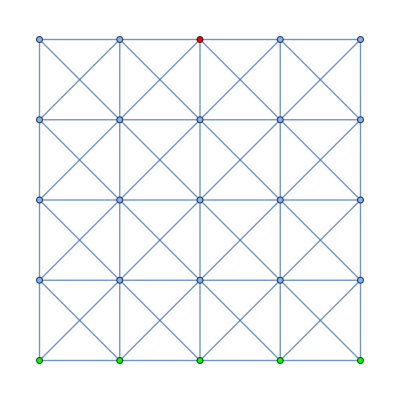

```mathematica
g = NearestNeighborGraph[Catenate[Table[{i, j}, {i, 1, 5}, {j, 1, 5}]],{All,Sqrt[2]}, VertexCoordinates->Catenate[Table[{i, j}, {i, 1, 5}, {j, 1, 5}]], VertexStyle->Join[{{3, 5}->Red}, Table[{i, 1}->Green, {i, 1, 5}]]]
```

```mathematica
FindPath[g,{3, 5},{1, 1},4, 1]
```

{{{3,5},{1,3},{1,1}}}

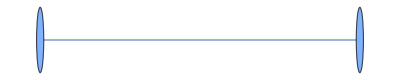

```mathematica
PathGraph[First[ps]]
```

```mathematica
ps[[1]]
```

{{1,1},{1,2}}

```mathematica
Partition[First[ps], 2, 1]
```

{{{1,1},{1,2}}}

{{1,1}->{1,2}}

```mathematica
#1->#2&@@@Partition[First[FindPath[g,{3, 5},{1, 1},5,All]], 2, 1]
```

{{3,5}→{4,4},{4,4}→{3,3},{3,3}→{2,2},{2,2}→{1,1}}

```mathematica
FindShortestPath[g, {3, 5}, {{1,1}, {1, 2}}]
```

FindShortestPath::inv: The argument {{1,1},{1,2}} in FindShortestPath[Graph[<25>, <72>], {3, 5}, {{1, 1}, {1, 2}}] is not a valid vertex.

FindShortestPath[-Graphics-,{3,5},{{1,1},{1,2}}]

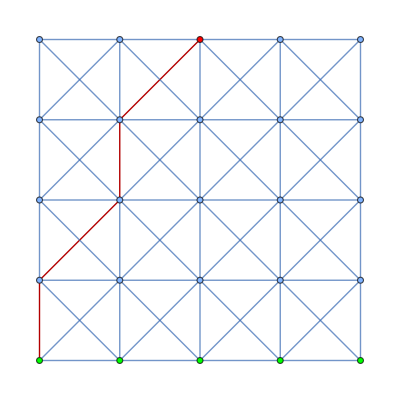
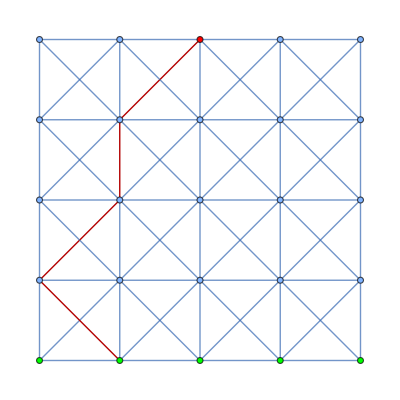
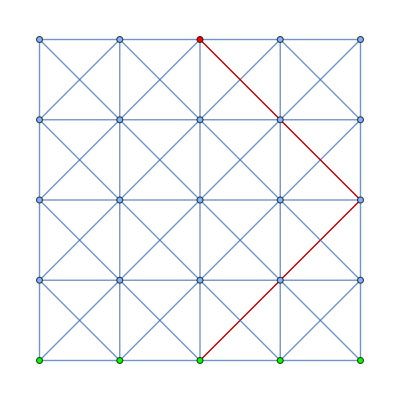
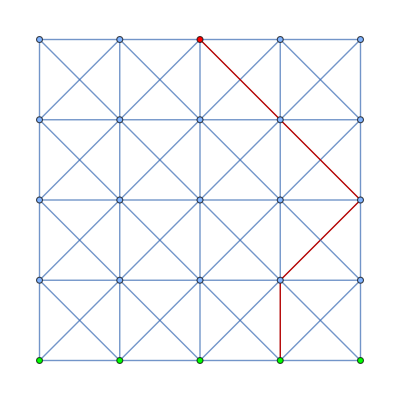
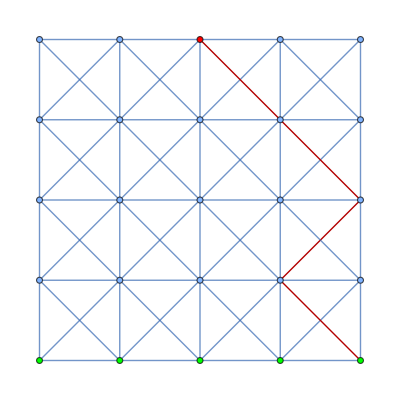

```mathematica
HighlightGraph[g, #]&/@(#1->#2&@@@Partition[#, 2, 1]&/@FindShortestPath[g, {3, 5}, All]/@Table[{i, 1},{i, 5}])
```

```mathematica
FindPath[g,{3, 5},{1, 1},5, All]
```

{{{3,5},{4,4},{3,3},{2,2},{1,1}},{{3,5},{3,4},{3,3},{2,2},{1,1}},{{3,5},{3,4},{2,3},{2,2},{1,1}},{{3,5},{3,4},{2,3},{1,2},{1,1}},{{3,5},{2,4},{3,3},{2,2},{1,1}},{{3,5},{2,4},{2,3},{2,2},{1,1}},{{3,5},{2,4},{2,3},{1,2},{1,1}},{{3,5},{2,4},{1,3},{2,2},{1,1}},{{3,5},{2,4},{1,3},{1,2},{1,1}},{{3,5},{4,5},{4,4},{3,3},{2,2},{1,1}},{{3,5},{4,5},{3,4},{3,3},{2,2},{1,1}},{{3,5},{4,5},{3,4},{2,3},{2,2},{1,1}},{{3,5},{4,5},{3,4},{2,3},{1,2},{1,1}},{{3,5},{4,4},{4,3},{3,3},{2,2},{1,1}},{{3,5},{4,4},{4,3},{3,2},{2,2},{1,1}},{{3,5},{4,4},{4,3},{3,2},{2,1},{1,1}},{{3,5},{4,4},{3,4},{3,3},{2,2},{1,1}},{{3,5},{4,4},{3,4},{2,3},{2,2},{1,1}},{{3,5},{4,4},{3,4},{2,3},{1,2},{1,1}},{{3,5},{4,4},{3,3},{3,2},{2,2},{1,1}},{{3,5},{4,4},{3,3},{3,2},{2,1},{1,1}},{{3,5},{4,4},{3,3},{2,3},{2,2},{1,1}},{{3,5},{4,4},{3,3},{2,3},{1,2},{1,1}},{{3,5},{4,4},{3,3},{2,2},{2,1},{1,1}},{{3,5},{4,4},{3,3},{2,2},{1,2},{1,1}},{{3,5},{3,4},{4,4},{3,3},{2,2},{1,1}},{{3,5},{3,4},{4,3},{3,3},{2,2},{1,1}},{{3,5},{3,4},{4,3},{3,2},{2,2},{1,1}},{{3,5},{3,4},{4,3},{3,2},{2,1},{1,1}},{{3,5},{3,4},{3,3},{3,2},{2,2},{1,1}},{{3,5},{3,4},{3,3},{3,2},{2,1},{1,1}},{{3,5},{3,4},{3,3},{2,3},{2,2},{1,1}},{{3,5},{3,4},{3,3},{2,3},{1,2},{1,1}},{{3,5},{3,4},{3,3},{2,2},{2,1},{1,1}},{{3,5},{3,4},{3,3},{2,2},{1,2},{1,1}},{{3,5},{3,4},{2,4},{3,3},{2,2},{1,1}},{{3,5},{3,4},{2,4},{2,3},{2,2},{1,1}},{{3,5},{3,4},{2,4},{2,3},{1,2},{1,1}},{{3,5},{3,4},{2,4},{1,3},{2,2},{1,1}},{{3,5},{3,4},{2,4},{1,3},{1,2},{1,1}},{{3,5},{3,4},{2,3},{3,3},{2,2},{1,1}},{{3,5},{3,4},{2,3},{3,2},{2,2},{1,1}},{{3,5},{3,4},{2,3},{3,2},{2,1},{1,1}},{{3,5},{3,4},{2,3},{2,2},{2,1},{1,1}},{{3,5},{3,4},{2,3},{2,2},{1,2},{1,1}},{{3,5},{3,4},{2,3},{1,3},{2,2},{1,1}},{{3,5},{3,4},{2,3},{1,3},{1,2},{1,1}},{{3,5},{3,4},{2,3},{1,2},{2,2},{1,1}},{{3,5},{3,4},{2,3},{1,2},{2,1},{1,1}},{{3,5},{2,5},{3,4},{3,3},{2,2},{1,1}},{{3,5},{2,5},{3,4},{2,3},{2,2},{1,1}},{{3,5},{2,5},{3,4},{2,3},{1,2},{1,1}},{{3,5},{2,5},{2,4},{3,3},{2,2},{1,1}},{{3,5},{2,5},{2,4},{2,3},{2,2},{1,1}},{{3,5},{2,5},{2,4},{2,3},{1,2},{1,1}},{{3,5},{2,5},{2,4},{1,3},{2,2},{1,1}},{{3,5},{2,5},{2,4},{1,3},{1,2},{1,1}},{{3,5},{2,5},{1,4},{2,3},{2,2},{1,1}},{{3,5},{2,5},{1,4},{2,3},{1,2},{1,1}},{{3,5},{2,5},{1,4},{1,3},{2,2},{1,1}},{{3,5},{2,5},{1,4},{1,3},{1,2},{1,1}},{{3,5},{2,4},{3,4},{3,3},{2,2},{1,1}},{{3,5},{2,4},{3,4},{2,3},{2,2},{1,1}},{{3,5},{2,4},{3,4},{2,3},{1,2},{1,1}},{{3,5},{2,4},{3,3},{3,2},{2,2},{1,1}},{{3,5},{2,4},{3,3},{3,2},{2,1},{1,1}},{{3,5},{2,4},{3,3},{2,3},{2,2},{1,1}},{{3,5},{2,4},{3,3},{2,3},{1,2},{1,1}},{{3,5},{2,4},{3,3},{2,2},{2,1},{1,1}},{{3,5},{2,4},{3,3},{2,2},{1,2},{1,1}},{{3,5},{2,4},{2,3},{3,3},{2,2},{1,1}},{{3,5},{2,4},{2,3},{3,2},{2,2},{1,1}},{{3,5},{2,4},{2,3},{3,2},{2,1},{1,1}},{{3,5},{2,4},{2,3},{2,2},{2,1},{1,1}},{{3,5},{2,4},{2,3},{2,2},{1,2},{1,1}},{{3,5},{2,4},{2,3},{1,3},{2,2},{1,1}},{{3,5},{2,4},{2,3},{1,3},{1,2},{1,1}},{{3,5},{2,4},{2,3},{1,2},{2,2},{1,1}},{{3,5},{2,4},{2,3},{1,2},{2,1},{1,1}},{{3,5},{2,4},{1,4},{2,3},{2,2},{1,1}},{{3,5},{2,4},{1,4},{2,3},{1,2},{1,1}},{{3,5},{2,4},{1,4},{1,3},{2,2},{1,1}},{{3,5},{2,4},{1,4},{1,3},{1,2},{1,1}},{{3,5},{2,4},{1,3},{2,3},{2,2},{1,1}},{{3,5},{2,4},{1,3},{2,3},{1,2},{1,1}},{{3,5},{2,4},{1,3},{2,2},{2,1},{1,1}},{{3,5},{2,4},{1,3},{2,2},{1,2},{1,1}},{{3,5},{2,4},{1,3},{1,2},{2,2},{1,1}},{{3,5},{2,4},{1,3},{1,2},{2,1},{1,1}}}

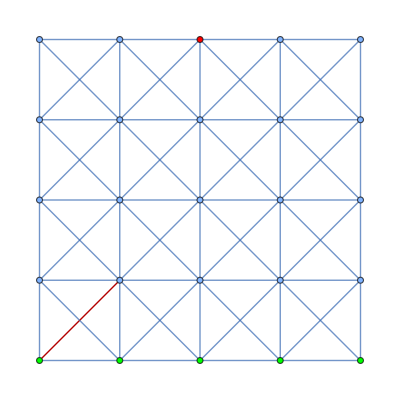

```mathematica
HighlightGraph[g, {{1, 1}->{2, 2}}]
```

```mathematica
EdgeList[g]
```

{{1,1}<->{1,2},{1,1}<->{2,1},{1,1}<->{2,2},{1,2}<->{1,3},{1,2}<->{2,1},{1,2}<->{2,2},{1,2}<->{2,3},{1,3}<->{1,4},{1,3}<->{2,2},{1,3}<->{2,3},{1,3}<->{2,4},{1,4}<->{1,5},{1,4}<->{2,3},{1,4}<->{2,4},{1,4}<->{2,5},{1,5}<->{2,4},{1,5}<->{2,5},{2,1}<->{2,2},{2,1}<->{3,1},{2,1}<->{3,2},{2,2}<->{2,3},{2,2}<->{3,1},{2,2}<->{3,2},{2,2}<->{3,3},{2,3}<->{2,4},{2,3}<->{3,2},{2,3}<->{3,3},{2,3}<->{3,4},{2,4}<->{2,5},{2,4}<->{3,3},{2,4}<->{3,4},{2,4}<->{3,5},{2,5}<->{3,4},{2,5}<->{3,5},{3,1}<->{3,2},{3,1}<->{4,1},{3,1}<->{4,2},{3,2}<->{3,3},{3,2}<->{4,1},{3,2}<->{4,2},{3,2}<->{4,3},{3,3}<->{3,4},{3,3}<->{4,2},{3,3}<->{4,3},{3,3}<->{4,4},{3,4}<->{3,5},{3,4}<->{4,3},{3,4}<->{4,4},{3,4}<->{4,5},{3,5}<->{4,4},{3,5}<->{4,5},{4,1}<->{4,2},{4,1}<->{5,1},{4,1}<->{5,2},{4,2}<->{4,3},{4,2}<->{5,1},{4,2}<->{5,2},{4,2}<->{5,3},{4,3}<->{4,4},{4,3}<->{5,2},{4,3}<->{5,3},{4,3}<->{5,4},{4,4}<->{4,5},{4,4}<->{5,3},{4,4}<->{5,4},{4,4}<->{5,5},{4,5}<->{5,4},{4,5}<->{5,5},{5,1}<->{5,2},{5,2}<->{5,3},{5,3}<->{5,4},{5,4}<->{5,5}}

```mathematica
FindPath[g,{3, 5},{1, 1},4,All]
```

{{{3,5},{4,4},{3,3},{2,2},{1,1}},{{3,5},{3,4},{3,3},{2,2},{1,1}},{{3,5},{3,4},{2,3},{2,2},{1,1}},{{3,5},{3,4},{2,3},{1,2},{1,1}},{{3,5},{2,4},{3,3},{2,2},{1,1}},{{3,5},{2,4},{2,3},{2,2},{1,1}},{{3,5},{2,4},{2,3},{1,2},{1,1}},{{3,5},{2,4},{1,3},{2,2},{1,1}},{{3,5},{2,4},{1,3},{1,2},{1,1}}}

FindPath::inv: The argument {3,5} in FindPath[Graph[<25>, <40>], {3, 5}, {i, 1}, 4, 5] is not a valid vertex.

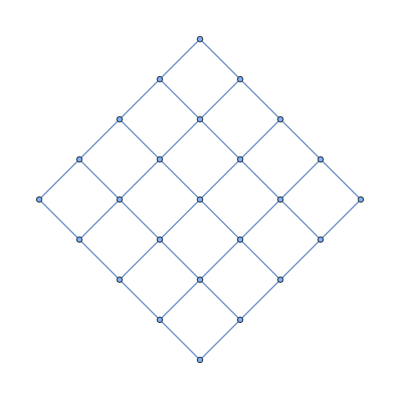
FindPath[-Graphics-,{3,5},{i,1},4,5]

```mathematica
FindPath[g,{3, 5},{i, 1},4,5]
```

```mathematica
ts = Tuples[Table[EuclideanDistance[#1, #2][#1->#2]&@@@Partition[#, 2, 1]&/@FindPath[g,{3, 5},{i, 1},4,5], {i, 5}]];
```

```mathematica
MinimalBy[Union@*Catenate/@ts, Total[Head/@#]&]
```

{{1[{2,2}→{2,1}],1[{2,3}→{2,2}],1[{2,4}→{2,3}],1[{3,2}→{3,1}],1[{3,3}→{3,2}],1[{4,2}→{4,1}],√2[{2,2}→{1,1}],√2[{2,4}→{3,3}],√2[{3,3}→{4,2}],√2[{3,5}→{2,4}],√2[{4,2}→{5,1}]}}

```mathematica
Head/@ts[[1]]
```

{List,List,List,List,List}

```mathematica
Head/@(Union@*Catenate/@ts)[[1]]
```

{1,1,1,1,1,√2,√2,√2,√2,√2,√2,√2,√2,√2,√2,√2}

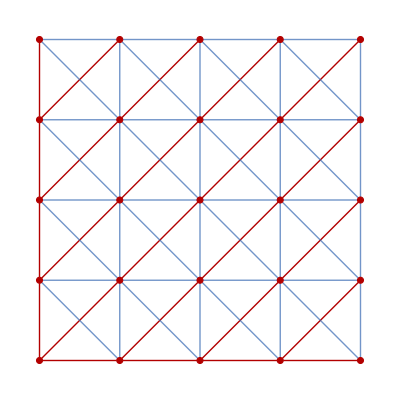

```mathematica
HighlightGraph[g, FindSpanningTree[g]]
```

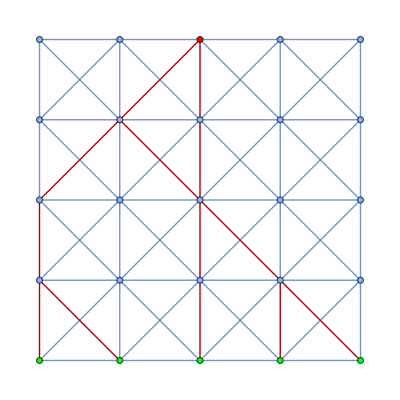
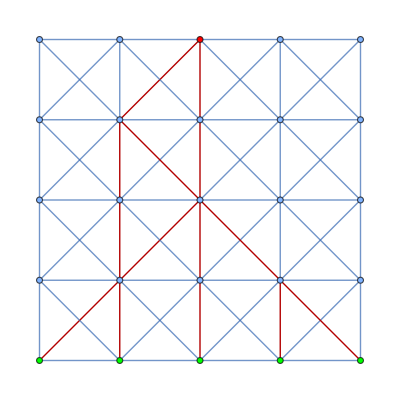
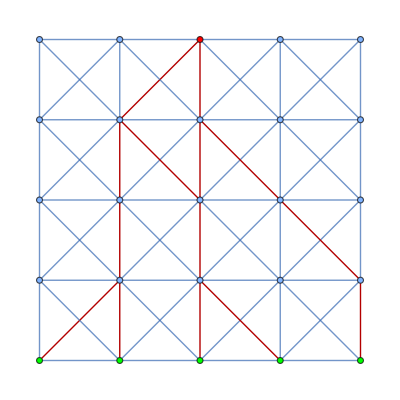
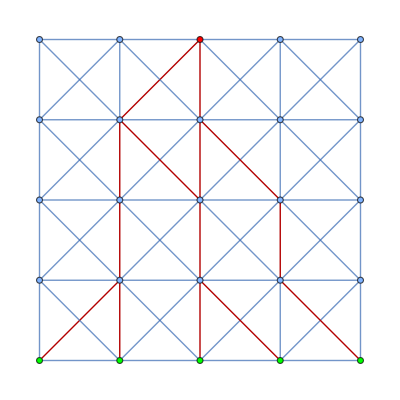
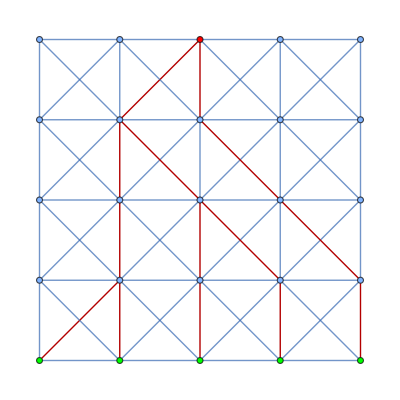
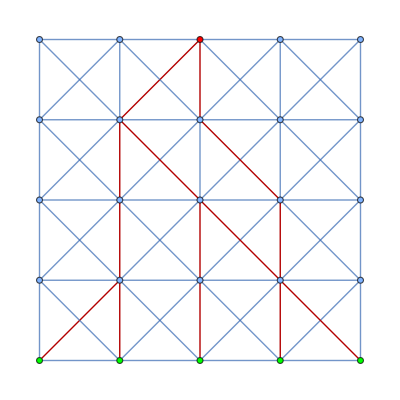
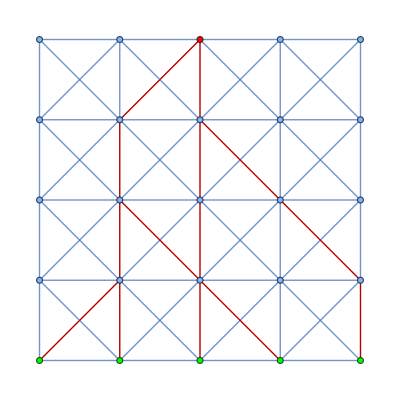
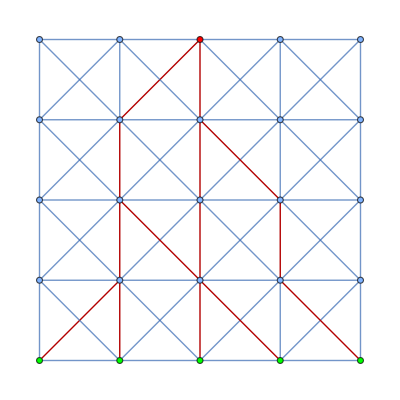
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
HighlightGraph[g,First/@ #]&/@MinimalBy[(Union@*Catenate/@ts), Total[Head/@#]&, 50][[40;;]]
```

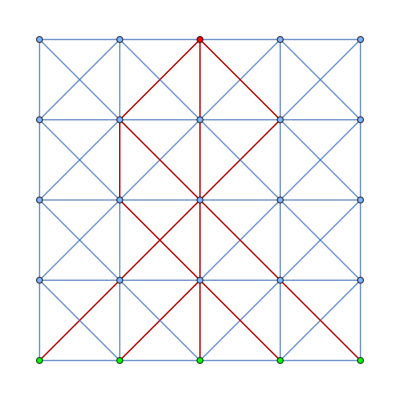

```mathematica
HighlightGraph[g, First/@(Union@*Catenate/@ts)[[1]]]
```

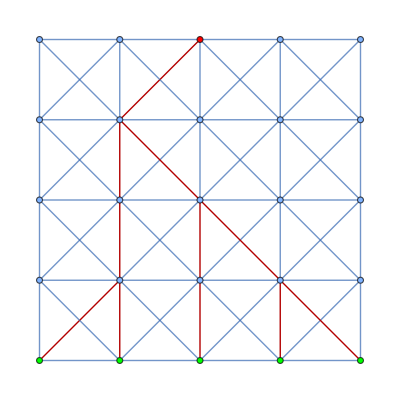

```mathematica
HighlightGraph[g, First/@#]&/@MinimalBy[Union@*Catenate/@ts, Total[Head/@#]&]
```

```mathematica
Length[ts]
```

3125

```mathematica
HighlightGraph[g, Catenate[ts[[1]]]]
```

-Graphics-

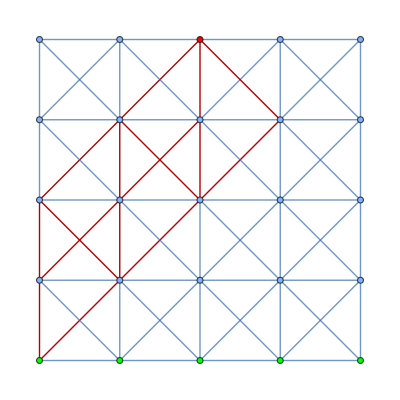

```mathematica
With[{ps = FindPath[g,{3, 5},{1, 1},5,All]},
HighlightGraph[g,Catenate[#1->#2&@@@Partition[#, 2, 1]&/@FindPath[g,{3, 5},{1, 1},4,All]]]]
```

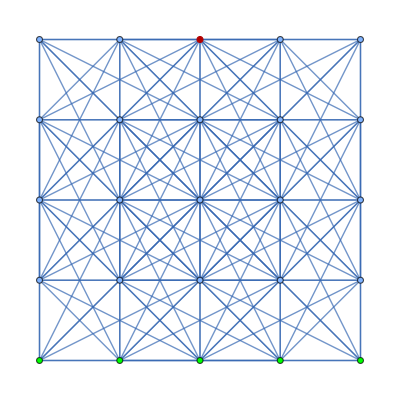

{{{3,5},{1,3},{1,1}},{{3,5},{1,3},{1,2},{1,1}},{{3,5},{1,3},{1,4},{2,2},{1,1}},{{3,5},{1,3},{1,4},{1,2},{1,1}},{{3,5},{1,3},{1,2},{3,3},{1,1}},{{3,5},{1,3},{1,2},{3,2},{1,1}},{{3,5},{1,3},{1,2},{3,1},{1,1}},{{3,5},{1,3},{1,2},{2,3},{1,1}},{{3,5},{1,3},{1,2},{2,2},{1,1}},{{3,5},{1,3},{1,2},{2,1},{1,1}}}

```mathematica
HighlightGraph[g, {3, 5}]
```

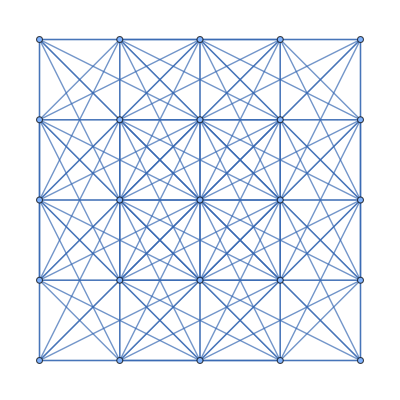

```mathematica
NearestNeighborGraph[Catenate[Table[{i, j}, {i, 1, 5}, {j, 1, 5}]], {All,2Sqrt[2]}, GraphLayout->"LayeredDigraphEmbedding"]
```

```mathematica
FindSpanningTree[Join[{{3, 5}}, Table[{i, 1}, {i, 1, 5}]]]
```

$Aborted

```mathematica
FindShortestPath[]
```

```mathematica
ps = Permutations[ Catenate[Table[{i, j}, {i, 1, 5}, {j, 1, 5}]], {2}];
```

```mathematica
ps
```

{{{1,1},{1,2}},{{1,1},{1,3}},{{1,1},{1,4}},{{1,1},{1,5}},{{1,1},{2,1}},{{1,1},{2,2}},{{1,1},{2,3}},{{1,1},{2,4}},{{1,1},{2,5}},{{1,1},{3,1}},{{1,1},{3,2}},{{1,1},{3,3}},{{1,1},{3,4}},{{1,1},{3,5}},{{1,1},{4,1}},{{1,1},{4,2}},{{1,1},{4,3}},{{1,1},{4,4}},{{1,1},{4,5}},{{1,1},{5,1}},{{1,1},{5,2}},{{1,1},{5,3}},{{1,1},{5,4}},{{1,1},{5,5}},{{1,2},{1,1}},{{1,2},{1,3}},{{1,2},{1,4}},{{1,2},{1,5}},{{1,2},{2,1}},{{1,2},{2,2}},{{1,2},{2,3}},{{1,2},{2,4}},{{1,2},{2,5}},{{1,2},{3,1}},{{1,2},{3,2}},{{1,2},{3,3}},{{1,2},{3,4}},{{1,2},{3,5}},{{1,2},{4,1}},{{1,2},{4,2}},{{1,2},{4,3}},{{1,2},{4,4}},{{1,2},{4,5}},{{1,2},{5,1}},{{1,2},{5,2}},{{1,2},{5,3}},{{1,2},{5,4}},{{1,2},{5,5}},{{1,3},{1,1}},{{1,3},{1,2}},{{1,3},{1,4}},{{1,3},{1,5}},{{1,3},{2,1}},{{1,3},{2,2}},{{1,3},{2,3}},{{1,3},{2,4}},{{1,3},{2,5}},{{1,3},{3,1}},{{1,3},{3,2}},{{1,3},{3,3}},{{1,3},{3,4}},{{1,3},{3,5}},{{1,3},{4,1}},{{1,3},{4,2}},{{1,3},{4,3}},{{1,3},{4,4}},{{1,3},{4,5}},{{1,3},{5,1}},{{1,3},{5,2}},{{1,3},{5,3}},{{1,3},{5,4}},{{1,3},{5,5}},{{1,4},{1,1}},{{1,4},{1,2}},{{1,4},{1,3}},{{1,4},{1,5}},{{1,4},{2,1}},{{1,4},{2,2}},{{1,4},{2,3}},{{1,4},{2,4}},{{1,4},{2,5}},{{1,4},{3,1}},{{1,4},{3,2}},{{1,4},{3,3}},{{1,4},{3,4}},{{1,4},{3,5}},{{1,4},{4,1}},{{1,4},{4,2}},{{1,4},{4,3}},{{1,4},{4,4}},{{1,4},{4,5}},{{1,4},{5,1}},{{1,4},{5,2}},{{1,4},{5,3}},{{1,4},{5,4}},{{1,4},{5,5}},{{1,5},{1,1}},{{1,5},{1,2}},{{1,5},{1,3}},{{1,5},{1,4}},{{1,5},{2,1}},{{1,5},{2,2}},{{1,5},{2,3}},{{1,5},{2,4}},{{1,5},{2,5}},{{1,5},{3,1}},{{1,5},{3,2}},{{1,5},{3,3}},{{1,5},{3,4}},{{1,5},{3,5}},{{1,5},{4,1}},{{1,5},{4,2}},{{1,5},{4,3}},{{1,5},{4,4}},{{1,5},{4,5}},{{1,5},{5,1}},{{1,5},{5,2}},{{1,5},{5,3}},{{1,5},{5,4}},{{1,5},{5,5}},{{2,1},{1,1}},{{2,1},{1,2}},{{2,1},{1,3}},{{2,1},{1,4}},{{2,1},{1,5}},{{2,1},{2,2}},{{2,1},{2,3}},{{2,1},{2,4}},{{2,1},{2,5}},{{2,1},{3,1}},{{2,1},{3,2}},{{2,1},{3,3}},{{2,1},{3,4}},{{2,1},{3,5}},{{2,1},{4,1}},{{2,1},{4,2}},{{2,1},{4,3}},{{2,1},{4,4}},{{2,1},{4,5}},{{2,1},{5,1}},{{2,1},{5,2}},{{2,1},{5,3}},{{2,1},{5,4}},{{2,1},{5,5}},{{2,2},{1,1}},{{2,2},{1,2}},{{2,2},{1,3}},{{2,2},{1,4}},{{2,2},{1,5}},{{2,2},{2,1}},{{2,2},{2,3}},{{2,2},{2,4}},{{2,2},{2,5}},{{2,2},{3,1}},{{2,2},{3,2}},{{2,2},{3,3}},{{2,2},{3,4}},{{2,2},{3,5}},{{2,2},{4,1}},{{2,2},{4,2}},{{2,2},{4,3}},{{2,2},{4,4}},{{2,2},{4,5}},{{2,2},{5,1}},{{2,2},{5,2}},{{2,2},{5,3}},{{2,2},{5,4}},{{2,2},{5,5}},{{2,3},{1,1}},{{2,3},{1,2}},{{2,3},{1,3}},{{2,3},{1,4}},{{2,3},{1,5}},{{2,3},{2,1}},{{2,3},{2,2}},{{2,3},{2,4}},{{2,3},{2,5}},{{2,3},{3,1}},{{2,3},{3,2}},{{2,3},{3,3}},{{2,3},{3,4}},{{2,3},{3,5}},{{2,3},{4,1}},{{2,3},{4,2}},{{2,3},{4,3}},{{2,3},{4,4}},{{2,3},{4,5}},{{2,3},{5,1}},{{2,3},{5,2}},{{2,3},{5,3}},{{2,3},{5,4}},{{2,3},{5,5}},{{2,4},{1,1}},{{2,4},{1,2}},{{2,4},{1,3}},{{2,4},{1,4}},{{2,4},{1,5}},{{2,4},{2,1}},{{2,4},{2,2}},{{2,4},{2,3}},{{2,4},{2,5}},{{2,4},{3,1}},{{2,4},{3,2}},{{2,4},{3,3}},{{2,4},{3,4}},{{2,4},{3,5}},{{2,4},{4,1}},{{2,4},{4,2}},{{2,4},{4,3}},{{2,4},{4,4}},{{2,4},{4,5}},{{2,4},{5,1}},{{2,4},{5,2}},{{2,4},{5,3}},{{2,4},{5,4}},{{2,4},{5,5}},{{2,5},{1,1}},{{2,5},{1,2}},{{2,5},{1,3}},{{2,5},{1,4}},{{2,5},{1,5}},{{2,5},{2,1}},{{2,5},{2,2}},{{2,5},{2,3}},{{2,5},{2,4}},{{2,5},{3,1}},{{2,5},{3,2}},{{2,5},{3,3}},{{2,5},{3,4}},{{2,5},{3,5}},{{2,5},{4,1}},{{2,5},{4,2}},{{2,5},{4,3}},{{2,5},{4,4}},{{2,5},{4,5}},{{2,5},{5,1}},{{2,5},{5,2}},{{2,5},{5,3}},{{2,5},{5,4}},{{2,5},{5,5}},{{3,1},{1,1}},{{3,1},{1,2}},{{3,1},{1,3}},{{3,1},{1,4}},{{3,1},{1,5}},{{3,1},{2,1}},{{3,1},{2,2}},{{3,1},{2,3}},{{3,1},{2,4}},{{3,1},{2,5}},{{3,1},{3,2}},{{3,1},{3,3}},{{3,1},{3,4}},{{3,1},{3,5}},{{3,1},{4,1}},{{3,1},{4,2}},{{3,1},{4,3}},{{3,1},{4,4}},{{3,1},{4,5}},{{3,1},{5,1}},{{3,1},{5,2}},{{3,1},{5,3}},{{3,1},{5,4}},{{3,1},{5,5}},{{3,2},{1,1}},{{3,2},{1,2}},{{3,2},{1,3}},{{3,2},{1,4}},{{3,2},{1,5}},{{3,2},{2,1}},{{3,2},{2,2}},{{3,2},{2,3}},{{3,2},{2,4}},{{3,2},{2,5}},{{3,2},{3,1}},{{3,2},{3,3}},{{3,2},{3,4}},{{3,2},{3,5}},{{3,2},{4,1}},{{3,2},{4,2}},{{3,2},{4,3}},{{3,2},{4,4}},{{3,2},{4,5}},{{3,2},{5,1}},{{3,2},{5,2}},{{3,2},{5,3}},{{3,2},{5,4}},{{3,2},{5,5}},{{3,3},{1,1}},{{3,3},{1,2}},{{3,3},{1,3}},{{3,3},{1,4}},{{3,3},{1,5}},{{3,3},{2,1}},{{3,3},{2,2}},{{3,3},{2,3}},{{3,3},{2,4}},{{3,3},{2,5}},{{3,3},{3,1}},{{3,3},{3,2}},{{3,3},{3,4}},{{3,3},{3,5}},{{3,3},{4,1}},{{3,3},{4,2}},{{3,3},{4,3}},{{3,3},{4,4}},{{3,3},{4,5}},{{3,3},{5,1}},{{3,3},{5,2}},{{3,3},{5,3}},{{3,3},{5,4}},{{3,3},{5,5}},{{3,4},{1,1}},{{3,4},{1,2}},{{3,4},{1,3}},{{3,4},{1,4}},{{3,4},{1,5}},{{3,4},{2,1}},{{3,4},{2,2}},{{3,4},{2,3}},{{3,4},{2,4}},{{3,4},{2,5}},{{3,4},{3,1}},{{3,4},{3,2}},{{3,4},{3,3}},{{3,4},{3,5}},{{3,4},{4,1}},{{3,4},{4,2}},{{3,4},{4,3}},{{3,4},{4,4}},{{3,4},{4,5}},{{3,4},{5,1}},{{3,4},{5,2}},{{3,4},{5,3}},{{3,4},{5,4}},{{3,4},{5,5}},{{3,5},{1,1}},{{3,5},{1,2}},{{3,5},{1,3}},{{3,5},{1,4}},{{3,5},{1,5}},{{3,5},{2,1}},{{3,5},{2,2}},{{3,5},{2,3}},{{3,5},{2,4}},{{3,5},{2,5}},{{3,5},{3,1}},{{3,5},{3,2}},{{3,5},{3,3}},{{3,5},{3,4}},{{3,5},{4,1}},{{3,5},{4,2}},{{3,5},{4,3}},{{3,5},{4,4}},{{3,5},{4,5}},{{3,5},{5,1}},{{3,5},{5,2}},{{3,5},{5,3}},{{3,5},{5,4}},{{3,5},{5,5}},{{4,1},{1,1}},{{4,1},{1,2}},{{4,1},{1,3}},{{4,1},{1,4}},{{4,1},{1,5}},{{4,1},{2,1}},{{4,1},{2,2}},{{4,1},{2,3}},{{4,1},{2,4}},{{4,1},{2,5}},{{4,1},{3,1}},{{4,1},{3,2}},{{4,1},{3,3}},{{4,1},{3,4}},{{4,1},{3,5}},{{4,1},{4,2}},{{4,1},{4,3}},{{4,1},{4,4}},{{4,1},{4,5}},{{4,1},{5,1}},{{4,1},{5,2}},{{4,1},{5,3}},{{4,1},{5,4}},{{4,1},{5,5}},{{4,2},{1,1}},{{4,2},{1,2}},{{4,2},{1,3}},{{4,2},{1,4}},{{4,2},{1,5}},{{4,2},{2,1}},{{4,2},{2,2}},{{4,2},{2,3}},{{4,2},{2,4}},{{4,2},{2,5}},{{4,2},{3,1}},{{4,2},{3,2}},{{4,2},{3,3}},{{4,2},{3,4}},{{4,2},{3,5}},{{4,2},{4,1}},{{4,2},{4,3}},{{4,2},{4,4}},{{4,2},{4,5}},{{4,2},{5,1}},{{4,2},{5,2}},{{4,2},{5,3}},{{4,2},{5,4}},{{4,2},{5,5}},{{4,3},{1,1}},{{4,3},{1,2}},{{4,3},{1,3}},{{4,3},{1,4}},{{4,3},{1,5}},{{4,3},{2,1}},{{4,3},{2,2}},{{4,3},{2,3}},{{4,3},{2,4}},{{4,3},{2,5}},{{4,3},{3,1}},{{4,3},{3,2}},{{4,3},{3,3}},{{4,3},{3,4}},{{4,3},{3,5}},{{4,3},{4,1}},{{4,3},{4,2}},{{4,3},{4,4}},{{4,3},{4,5}},{{4,3},{5,1}},{{4,3},{5,2}},{{4,3},{5,3}},{{4,3},{5,4}},{{4,3},{5,5}},{{4,4},{1,1}},{{4,4},{1,2}},{{4,4},{1,3}},{{4,4},{1,4}},{{4,4},{1,5}},{{4,4},{2,1}},{{4,4},{2,2}},{{4,4},{2,3}},{{4,4},{2,4}},{{4,4},{2,5}},{{4,4},{3,1}},{{4,4},{3,2}},{{4,4},{3,3}},{{4,4},{3,4}},{{4,4},{3,5}},{{4,4},{4,1}},{{4,4},{4,2}},{{4,4},{4,3}},{{4,4},{4,5}},{{4,4},{5,1}},{{4,4},{5,2}},{{4,4},{5,3}},{{4,4},{5,4}},{{4,4},{5,5}},{{4,5},{1,1}},{{4,5},{1,2}},{{4,5},{1,3}},{{4,5},{1,4}},{{4,5},{1,5}},{{4,5},{2,1}},{{4,5},{2,2}},{{4,5},{2,3}},{{4,5},{2,4}},{{4,5},{2,5}},{{4,5},{3,1}},{{4,5},{3,2}},{{4,5},{3,3}},{{4,5},{3,4}},{{4,5},{3,5}},{{4,5},{4,1}},{{4,5},{4,2}},{{4,5},{4,3}},{{4,5},{4,4}},{{4,5},{5,1}},{{4,5},{5,2}},{{4,5},{5,3}},{{4,5},{5,4}},{{4,5},{5,5}},{{5,1},{1,1}},{{5,1},{1,2}},{{5,1},{1,3}},{{5,1},{1,4}},{{5,1},{1,5}},{{5,1},{2,1}},{{5,1},{2,2}},{{5,1},{2,3}},{{5,1},{2,4}},{{5,1},{2,5}},{{5,1},{3,1}},{{5,1},{3,2}},{{5,1},{3,3}},{{5,1},{3,4}},{{5,1},{3,5}},{{5,1},{4,1}},{{5,1},{4,2}},{{5,1},{4,3}},{{5,1},{4,4}},{{5,1},{4,5}},{{5,1},{5,2}},{{5,1},{5,3}},{{5,1},{5,4}},{{5,1},{5,5}},{{5,2},{1,1}},{{5,2},{1,2}},{{5,2},{1,3}},{{5,2},{1,4}},{{5,2},{1,5}},{{5,2},{2,1}},{{5,2},{2,2}},{{5,2},{2,3}},{{5,2},{2,4}},{{5,2},{2,5}},{{5,2},{3,1}},{{5,2},{3,2}},{{5,2},{3,3}},{{5,2},{3,4}},{{5,2},{3,5}},{{5,2},{4,1}},{{5,2},{4,2}},{{5,2},{4,3}},{{5,2},{4,4}},{{5,2},{4,5}},{{5,2},{5,1}},{{5,2},{5,3}},{{5,2},{5,4}},{{5,2},{5,5}},{{5,3},{1,1}},{{5,3},{1,2}},{{5,3},{1,3}},{{5,3},{1,4}},{{5,3},{1,5}},{{5,3},{2,1}},{{5,3},{2,2}},{{5,3},{2,3}},{{5,3},{2,4}},{{5,3},{2,5}},{{5,3},{3,1}},{{5,3},{3,2}},{{5,3},{3,3}},{{5,3},{3,4}},{{5,3},{3,5}},{{5,3},{4,1}},{{5,3},{4,2}},{{5,3},{4,3}},{{5,3},{4,4}},{{5,3},{4,5}},{{5,3},{5,1}},{{5,3},{5,2}},{{5,3},{5,4}},{{5,3},{5,5}},{{5,4},{1,1}},{{5,4},{1,2}},{{5,4},{1,3}},{{5,4},{1,4}},{{5,4},{1,5}},{{5,4},{2,1}},{{5,4},{2,2}},{{5,4},{2,3}},{{5,4},{2,4}},{{5,4},{2,5}},{{5,4},{3,1}},{{5,4},{3,2}},{{5,4},{3,3}},{{5,4},{3,4}},{{5,4},{3,5}},{{5,4},{4,1}},{{5,4},{4,2}},{{5,4},{4,3}},{{5,4},{4,4}},{{5,4},{4,5}},{{5,4},{5,1}},{{5,4},{5,2}},{{5,4},{5,3}},{{5,4},{5,5}},{{5,5},{1,1}},{{5,5},{1,2}},{{5,5},{1,3}},{{5,5},{1,4}},{{5,5},{1,5}},{{5,5},{2,1}},{{5,5},{2,2}},{{5,5},{2,3}},{{5,5},{2,4}},{{5,5},{2,5}},{{5,5},{3,1}},{{5,5},{3,2}},{{5,5},{3,3}},{{5,5},{3,4}},{{5,5},{3,5}},{{5,5},{4,1}},{{5,5},{4,2}},{{5,5},{4,3}},{{5,5},{4,4}},{{5,5},{4,5}},{{5,5},{5,1}},{{5,5},{5,2}},{{5,5},{5,3}},{{5,5},{5,4}}}

```mathematica
apes = Permutations[]
```

### gpt version

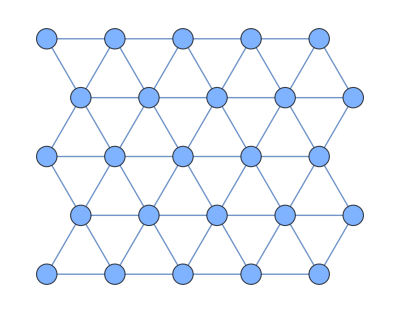

```mathematica
(*Create 25 points in a 2D triangular-lattice arrangement.*)points=Flatten[Table[{i+0.5*Mod[j,2],(Sqrt[3]/2) j},{j,0,4},{i,0,4}],1];

(*Connect each point to all neighbors within distance~1.0.*)
g=NearestNeighborGraph[points,{All,1.1}];

Graph[g,VertexCoordinates->points,PlotRange->All,VertexSize->0.3]
```

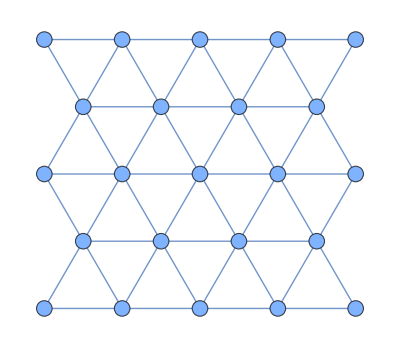

```mathematica
(*1) Generate the full 5×5 triangular-lattice points.*)pointsAll=Flatten[Table[{i+0.5*Mod[j,2],(Sqrt[3]/2) j},{j,0,4},(*j=rows*){i,0,4}   (*i=columns*)],1];

(*2) Keep all points except those at x=4.5.*)
points=Select[pointsAll,#[[1]]<4.5&];

(*3) Connect each point to neighbors within~1 unit.*)
g=NearestNeighborGraph[points,{All,1.1}];

(*4) Draw the graph,placing each vertex at the exact coordinate.*)
g2 = Graph[g,VertexCoordinates->points,PlotRange->All,VertexSize->0.2]
```

FindShortestPath::inv: The argument {3,5} in FindShortestPath[Graph[<23>, <50>], {3, 5}, {{1, 1}, {2, 1}, {3, 1}, {4, 1}, {5, 1}}] is not a valid vertex.

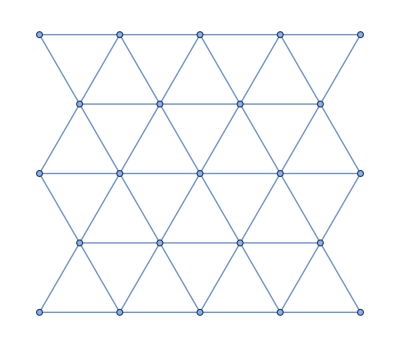
FindShortestPath[-Graphics-,{3,5},{{1,1},{2,1},{3,1},{4,1},{5,1}}]

```mathematica
FindShortestPath[g, {3, 5}, Table[{i, 1}, {i, 1, 5}]]
```

NearestFunction::mepcmp: Internal extra precision limit $MaxExtraPrecision reached for some distance comparisons.  These distances were taken as equal even though strict equality was not verified.  Increasing the value of $MaxExtraPrecision may resolve the uncertainty.

General::stop: Further output of NearestFunction::mepcmp will be suppressed during this calculation.

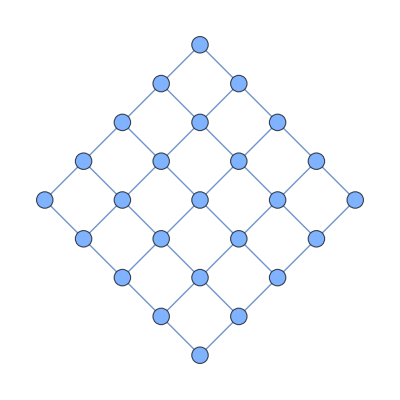

```mathematica
(*1) Define two lattice vectors of length 1,meeting at 90°.Here we pick vectors that form a'diamond' shape when plotted.*)a={1/Sqrt[2],1/Sqrt[2]};   (*45° upward-right*)
b={1/Sqrt[2],-1/Sqrt[2]};   (*45° downward-right*)

(*2) Generate a 5×5 grid of points using integer combinations of a and b.*)
points=Flatten[Table[i a+j b,(*coordinates in R^2*){i,0,4},{j,0,4}],1];

(*3) Build a graph by connecting each point to all others within distance~1.*)
g=NearestNeighborGraph[points,{All,1.05}];

(*4) Draw the graph with those exact coordinates.*)
Graph[g,VertexCoordinates->points,PlotRange->All,VertexSize->0.3]
```

### V2

```mathematica
g = NearestNeighborGraph[Catenate[Table[{i, j}, {i, 1, 5}, {j, 1, 5}]],{All,Sqrt[2]}, VertexCoordinates->Catenate[Table[{i, j}, {i, 1, 5}, {j, 1, 5}]], VertexStyle->Join[{{3, 5}->Red}, Table[{i, 1}->Green, {i, 1, 5}]]]
```

```mathematica
FindPath[g,{3, 5},{1, 1},3,10]
```

```mathematica
tab = Table[EuclideanDistance[#1, #2][#1->#2]&@@@Partition[#, 2, 1]&/@FindPath[g,{3, 5},{i, 1},4,10], {i, 5}];
```

```mathematica
First/@Catenate[ts10[[1]]]
```

{{3,5}→{4,4},{4,4}→{3,3},{3,3}→{2,2},{2,2}→{1,1},{3,5}→{3,4},{3,4}→{2,3},{2,3}→{3,2},{3,2}→{2,1},{3,5}→{3,4},{3,4}→{3,3},{3,3}→{3,2},{3,2}→{3,1},{3,5}→{4,4},{4,4}→{3,3},{3,3}→{3,2},{3,2}→{4,1},{3,5}→{4,4},{4,4}→{5,3},{5,3}→{5,2},{5,2}→{5,1}}

```mathematica
ts10 = Tuples[tab];
```

```mathematica
First/@Intersection[Catenate[ts10[[1]]]]
```

{{3,2}→{3,1},{3,3}→{3,2},{3,4}→{3,3},{3,5}→{3,4},{5,2}→{5,1},{5,3}→{5,2},{2,2}→{1,1},{2,3}→{3,2},{3,2}→{2,1},{3,2}→{4,1},{3,3}→{2,2},{3,4}→{2,3},{3,5}→{4,4},{4,4}→{3,3},{4,4}→{5,3}}

```mathematica
is = Intersection[Catenate[#]]&/@ ts10;
```

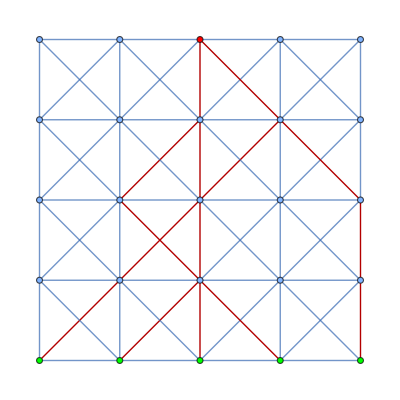

```mathematica
HighlightGraph[g, First/@Intersection[Catenate[ts10[[1]]]]]
```

```mathematica
o = EuclideanDistance[#[[1]], #[[2]]][#]&/@{{3, 5}-> {3, 4}, {3, 4}-> {3,3}, {3, 3}-> {2, 2}, {3, 3}-> {3, 2}, {3, 3}-> {4, 2}, {2, 2}-> {1, 1}, {2, 2}->{2, 1}, {3, 2}->{3, 1}, {4, 2}-> {4, 1}, {4, 2}->{5, 2}};
```

```mathematica
N@Total[Head/@o]
```

11.2426

```mathematica
N[Total[Head/@#]]&/@MinimalBy[is, Total[Head/@#]&, 10]
```

{12.6569,13.6569,13.6569,13.6569,14.6569,14.6569,14.6569,14.6569,15.6569,15.6569}

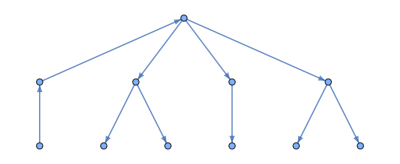

```mathematica
Graph[o]
```

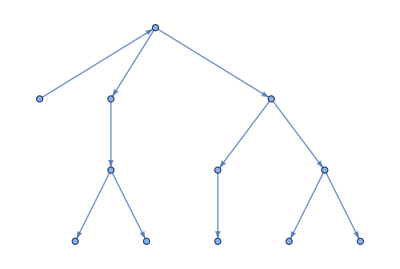
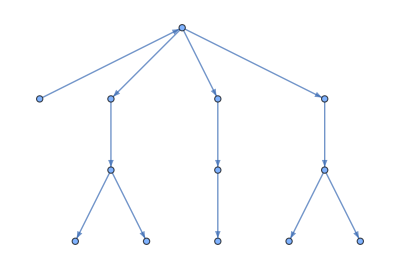
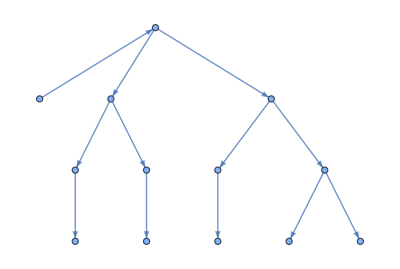
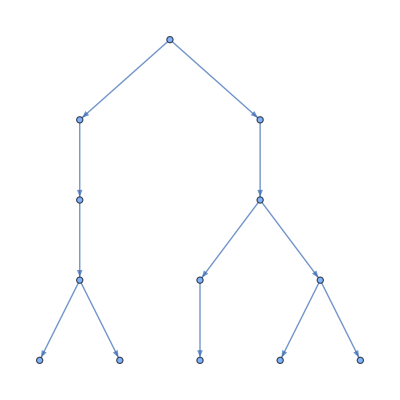
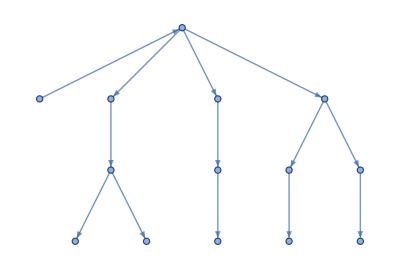
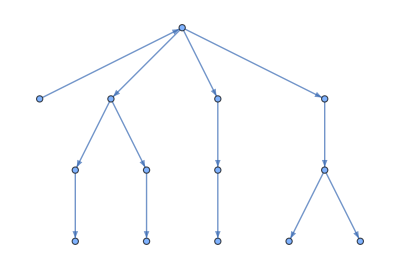
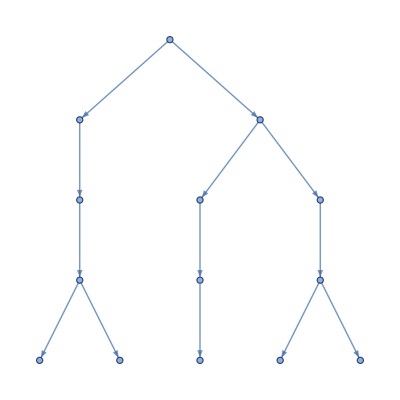
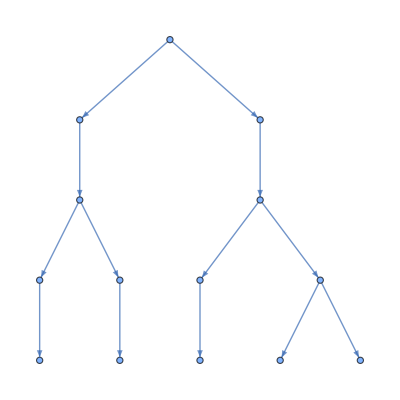

```mathematica
Graph[First/@#]&/@MinimalBy[is, Total[Head/@#]&, 10]
```

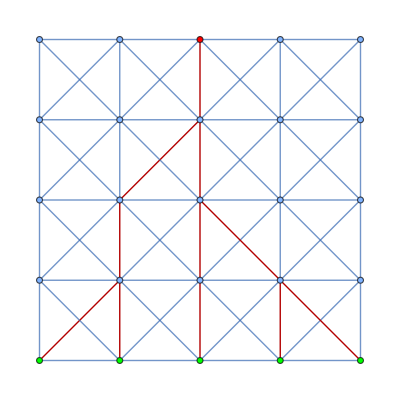
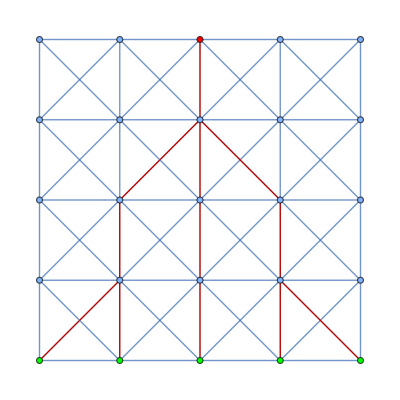
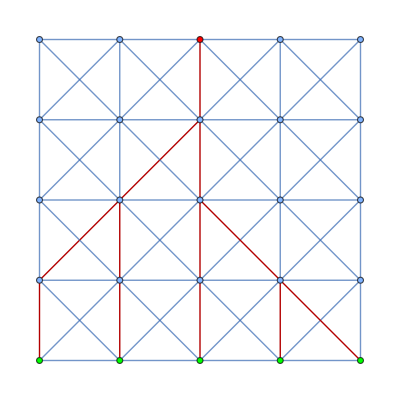
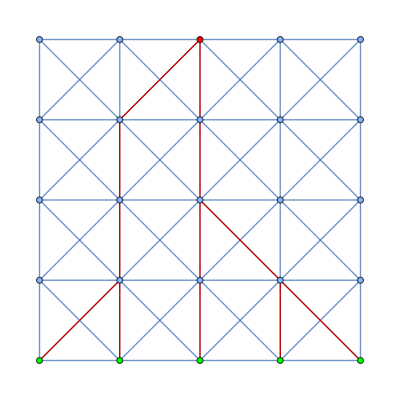
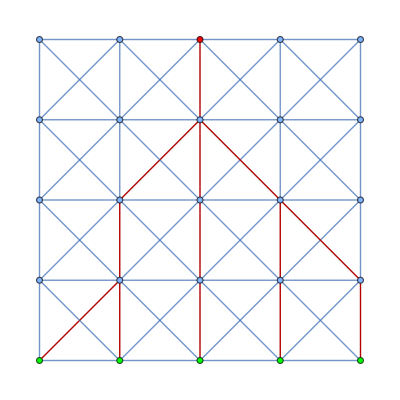
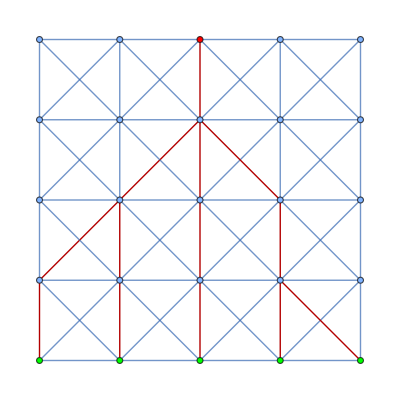
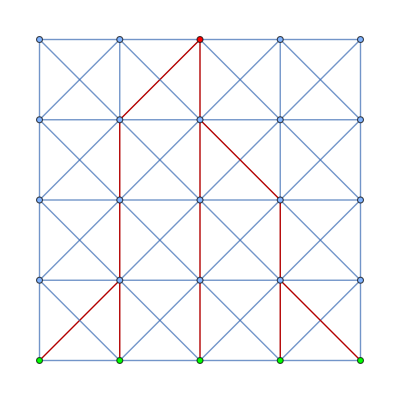
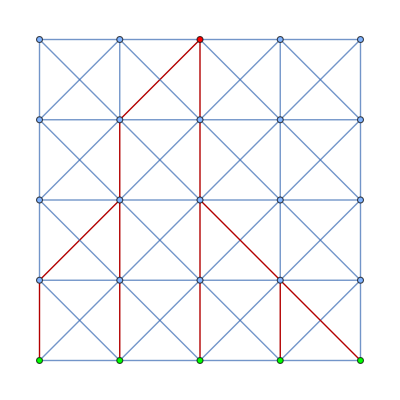

```mathematica
HighlightGraph[g, First/@#]&/@MinimalBy[is, Total[Head/@#]&, 10]
```

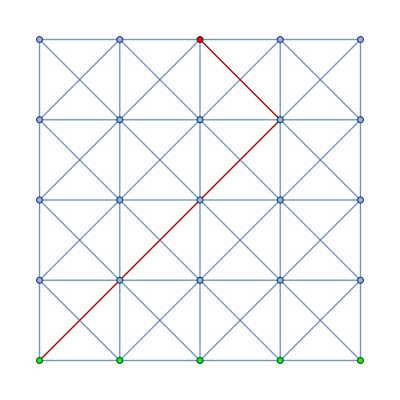
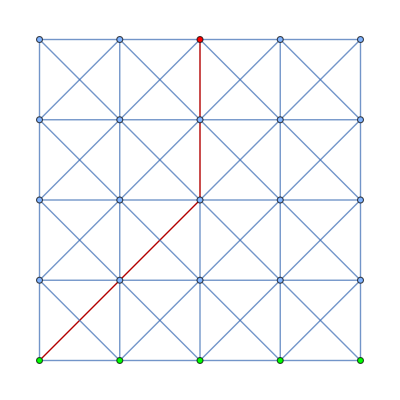
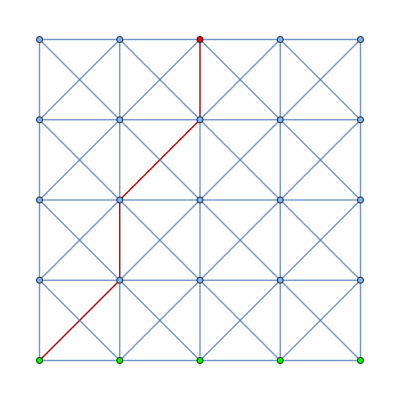
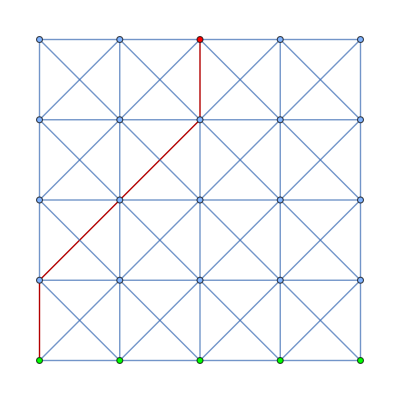
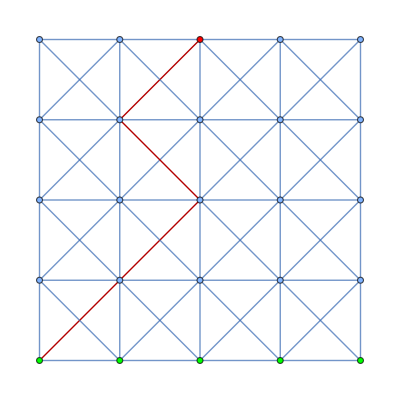
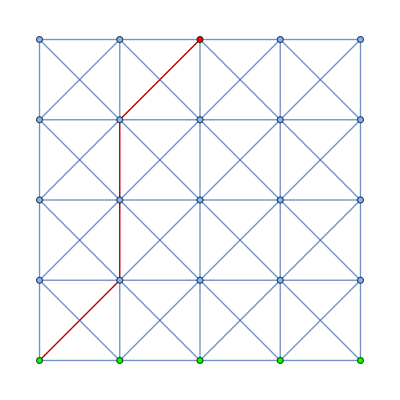
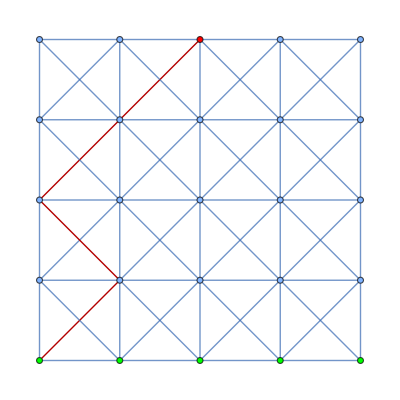
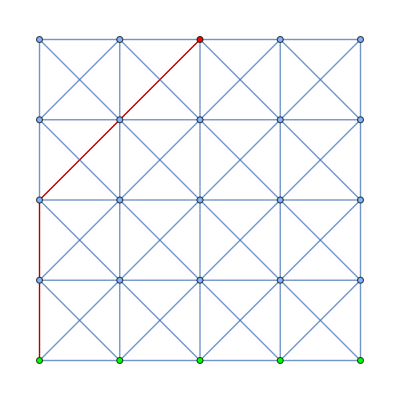
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
HighlightGraph[g,First/@ #]&/@tab[[1]]
```

```mathematica
ts = Tuples[Table[EuclideanDistance[#1, #2][#1->#2]&@@@Partition[#, 2, 1]&/@FindPath[g,{3, 5},{i, 1},4,10], {i, 5}]];
```

```mathematica
HighlightGraph[g,First/@ #]&/@MinimalBy[(Union@*Catenate/@ts), Total[Head/@#]&, 5]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

### Trying pure square version

### Adaptive version

### with weights

### Placing a fixed number of edges

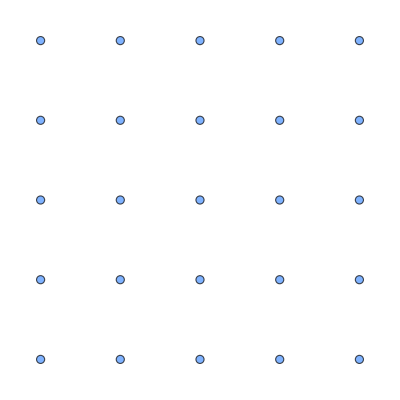

```mathematica
Graph[Catenate[Table[{i, j}, {i, 1, 5}, {j, 1, 5}]], {}]
```

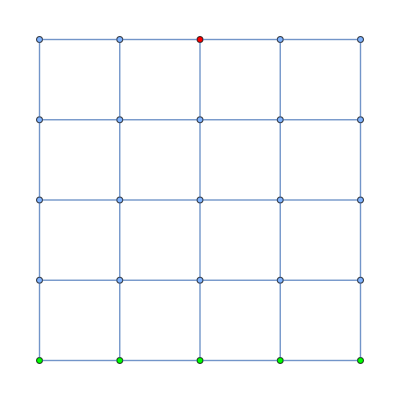

```mathematica
g = NearestNeighborGraph[Catenate[Table[{i, j}, {i, 1, 5}, {j, 1, 5}]],{All,1}, VertexCoordinates->Catenate[Table[{i, j}, {i, 1, 5}, {j, 1, 5}]], VertexStyle->Join[{{3, 5}->Red}, Table[{i, 1}->Green, {i, 1, 5}]]]
```

```mathematica
EdgeList[g] // Length
```

40

```mathematica
Permutations[EdgeList[g], {20}]
```

Permutations::len: Permutations[{{1,1}<->{1,2},{1,1}<->{2,1},{1,2}<->{1,3},{1,2}<->{2,2},{1,3}<->{1,4},{1,3}<->{2,3},{1,4}<->{1,5},{1,4}<->{2,4},{1,5}<->{2,5},{2,1}<->{2,2},{2,1}<->{3,1},{2,2}<->{2,3},{2,2}<->{3,2},«15»,{4,1}<->{5,1},{4,2}<->{4,3},{4,2}<->{5,2},{4,3}<->{4,4},{4,3}<->{5,3},{4,4}<->{4,5},{4,4}<->{5,4},{4,5}<->{5,5},{5,1}<->{5,2},{5,2}<->{5,3},{5,3}<->{5,4},{5,4}<->{5,5}},{20}] cannot be computed because its length is 335367096786357081410764800000, which is not a machine integer.

Permutations[{{1,1}<->{1,2},{1,1}<->{2,1},{1,2}<->{1,3},{1,2}<->{2,2},{1,3}<->{1,4},{1,3}<->{2,3},{1,4}<->{1,5},{1,4}<->{2,4},{1,5}<->{2,5},{2,1}<->{2,2},{2,1}<->{3,1},{2,2}<->{2,3},{2,2}<->{3,2},{2,3}<->{2,4},{2,3}<->{3,3},{2,4}<->{2,5},{2,4}<->{3,4},{2,5}<->{3,5},{3,1}<->{3,2},{3,1}<->{4,1},{3,2}<->{3,3},{3,2}<->{4,2},{3,3}<->{3,4},{3,3}<->{4,3},{3,4}<->{3,5},{3,4}<->{4,4},{3,5}<->{4,5},{4,1}<->{4,2},{4,1}<->{5,1},{4,2}<->{4,3},{4,2}<->{5,2},{4,3}<->{4,4},{4,3}<->{5,3},{4,4}<->{4,5},{4,4}<->{5,4},{4,5}<->{5,5},{5,1}<->{5,2},{5,2}<->{5,3},{5,3}<->{5,4},{5,4}<->{5,5}},{20}]

```mathematica
ss = Subsets[EdgeList[g], {5}];
```

```mathematica
ss[[1]]
```

{{1,1}<->{1,2},{1,1}<->{2,1},{1,2}<->{1,3},{1,2}<->{2,2},{1,3}<->{1,4}}

```mathematica
Table[{i, 1}, {i, 1, 5}]
```

{{1,1},{2,1},{3,1},{4,1},{5,1}}

```mathematica
Point[{3, 5}]
```

Point[{3,5}]

```mathematica
Join[{Point[{3, 5}]}, Table[{i, 1}, {i, 1, 5}]]
```

{Point[{3,5}],{1,1},{2,1},{3,1},{4,1},{5,1}}

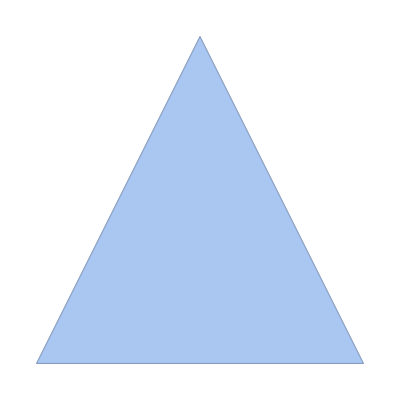

```mathematica
ConvexHullMesh[Join[{Point[{3, 5}]}, Table[Point[{i, 1}], {i, 1, 5}]]]
```

```mathematica
Graphics[Join[{Point[{3, 5}]},{Point[{1, 2}], Point[{5, 2}]},  Table[Point[{i, 1}], {i, 2, 4}]]]
```

-Graphics-

```mathematica
(*Define arc parameters*)r=5;                     (*Radius*)
θ1=0;                    (*Start angle (radians)*)
θ2=Pi/2;                 (*End angle (radians)*)
n=5;
```

```mathematica
arcPoints=Table[{r Cos[θ],r Sin[θ]},{θ,θ1,θ2,(θ2-θ1)/(n-1)}];
```

```mathematica
Graphics[Point/@arcPoints]
```

-Graphics-

```mathematica
(*Define arc parameters for the bottom half of a circle*)r=5;                      (*Radius*)
θ1=Pi;                    (*Start angle:leftmost point on the bottom*)
θ2=2 Pi;                  (*End angle:rightmost point on the bottom*)
n=5;                      (*Number of points*)

(*Generate n points along the bottom arc*)
arcPoints=Table[{2r Cos[θ],2r Sin[θ]},{θ,θ1,θ2,(θ2-θ1)/(n-1)}];

(*Plot the points on the arc*)
Graphics[{(*Draw bottom arc*)PointSize[Large],Point/@arcPoints             (*Draw points*)}]
```

-Graphics-

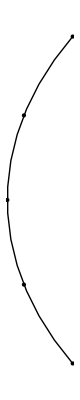

```mathematica
(*Define arc parameters for a shallower bottom curve*)r=5;                      (*Radius*)
θ1=(5 Pi)/6;              (*Start angle:slightly above π*)
θ2=(7 Pi)/6;              (*End angle:slightly below 2π*)
n=5;                      (*Number of points*)

(*Generate n points along the shallower bottom arc*)
arcPoints=Table[{r Cos[θ],r Sin[θ]},{θ,θ1,θ2,(θ2-θ1)/(n-1)}];

(*Plot the points on the arc*)
Graphics[{Circle[{0,0},r,{θ1,θ2}],(*Draw shallower arc*)PointSize[Large],Point/@arcPoints             (*Draw points*)}]
```

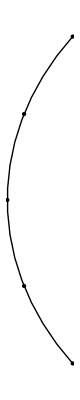

```mathematica
(*Define arc parameters for a flatter bottom curve*)r=5;                      (*Radius*)
θ1=(4 Pi)/5;              (*Start angle:slightly above π*)
θ2=(6 Pi)/5;              (*End angle:slightly below 2π*)
n=5;                      (*Number of points*)

(*Generate n points along the shallow bottom arc*)
arcPoints=Table[{r Cos[θ],r Sin[θ]},{θ,θ1,θ2,(θ2-θ1)/(n-1)}];

(*Plot the points on the arc*)
Graphics[{Circle[{0,0},r,{θ1,θ2}],(*Draw shallow arc*)PointSize[Large],Point/@arcPoints             (*Draw points*)}]
```

```mathematica
(*Define arc parameters for a shallow bottom-facing curve*)r=5;                      (*Radius of the arc*)
θ1=(8 Pi)/10;             (*Start angle:just above π*)
θ2=(12 Pi)/10;            (*End angle:just below π*)
n=8;                      (*Number of points*)

(*Generate points along the shallow bottom arc*)
arcPoints=Table[{r Sin[θ],-r Cos[θ]+3},(*Swap Sin and Cos to orient the arc correctly*){θ,θ1,θ2,(θ2-θ1)/(n-1)}];

(*Plot the points on the arc*)
Graphics[(*Draw the arc*){PointSize[Large],Point[{0, 0}],Point/@arcPoints             (*Draw the selected points*)}]
```

-Graphics-

```mathematica
{First@MinimalBy[arcPoints, First, 1],First@MaximalBy[arcPoints, First, 1]}
```

{{-5 √(5/8-(√5)/8),3-5/4 (-1-√5)},{5 Sin[π/7],3+5 Cos[π/7]}}

```mathematica
Graphics[Point/@]
```

-Graphics-

```mathematica
(*Given points A and B*)A={x1,y1};
B={x2,y2};

(*Given angle theta (in radians)*)
θ=Pi/4; (*Example:45 degrees*)

(*Compute the rotated point C*)
CC=RotationTransform[θ,B][A]

(*Output:{x3,y3} which is the third point*)
```

{x1/(√2)-y1/(√2)+1/2 (2 x2-√2 x2+√2 y2),x1/(√2)+y1/(√2)+1/2 (-√2 x2+2 y2-√2 y2)}

```mathematica
Graphics[{Sequence@@(Point/@{First@MinimalBy[arcPoints, First],First@MaximalBy[arcPoints, First]}), Red, Point@RotationTransform[Pi/4, {5 Sin[π/7],3+5 Cos[π/7]}][{-5 √(5/8-(√5)/8),3-5/4 (-1-√5)}]}]
```

-Graphics-

### Arc v2

```mathematica
θ1=(8 Pi)/10;       
r = 5 ;
θ2=(12 Pi)/10;         
n=8;                 
arcPoints=Table[{r Sin[θ],-r Cos[θ]+3},
{θ,θ1,θ2,(θ2-θ1)/(n-1)}];
Graphics[{PointSize[Large],Point[{0, 0}],Point/@arcPoints }]
```

-Graphics-

```mathematica
{First@MinimalBy[arcPoints, First, 1],First@MaximalBy[arcPoints, First, 1]}
```

{{-5 √(5/8-(√5)/8),3-5/4 (-1-√5)},{5 Sin[π/7],3+5 Cos[π/7]}}

```mathematica
Graphics[Point/@]
```

-Graphics-

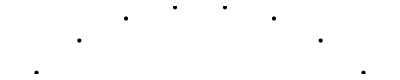

```mathematica
θ1=Pi-(Pi/5);  (*Start angle:symmetric around π*)
θ2=Pi+(Pi/5);  (*End angle*)
r=5;             (*Radius*)
n=8;             (*Number of points*)

arcPoints=Table[{r Sin[θ],-r Cos[θ]},(*Ensure symmetry with respect to π*){θ,θ1,θ2,(θ2-θ1)/(n-1)}];

Graphics[{PointSize[Large],Point/@arcPoints}]
```

```mathematica
{First@MinimalBy[arcPoints, First, 1],First@MaximalBy[arcPoints, First, 1]}
```

{{-5 √(5/8-(√5)/8),-5/4 (-1-√5)},{5 Sin[π/7],5 Cos[π/7]}}

```mathematica
Graphics[{PointSize[Large], Point[arcPoints[[{1, -1}]]], Red, Point@RotationTransform[Pi/4, arcPoints[[1]]][arcPoints[[-1]]]}]
```

-Graphics-

```mathematica
Graphics[{PointSize[Large], Point[arcPoints[[{1, -1}]]]}]
```

-Graphics-

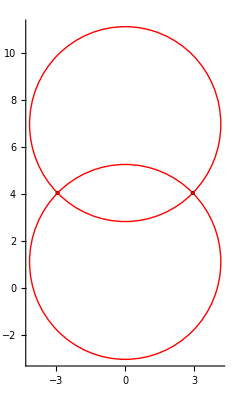

```mathematica
A=arcPoints[[1]];
B=arcPoints[[-1]];
(*1) Midpoint and distance*)
M=(A + B)/2;
d=EuclideanDistance[A,B];

(*2) Circle radius for 45° subtended angle*)
R=d/Sqrt[2];

(*3) Perp direction from midpoint*)
v=B-A;
p={v[[2]],-v[[1]]};      (*a perpendicular to v*)
pUnit=p/Norm[p];

center1=M+(d/2)*pUnit;
center2=M-(d/2)*pUnit;

Graphics[{PointSize[Large],Point[A],Point[B],Red,Circle[center1,R],Circle[center2,R]},PlotRange->All,Axes->True]
```

```mathematica
(*Find the center of the arc (midpoint of first and last points)*)arcCenter=Mean[{arcPoints[[1]],arcPoints[[-1]]}];

(*Rotate the last point around the arc center*)
rotatedPoint=RotationTransform[Pi/4,arcCenter][arcPoints[[-1]]];
```

```mathematica
(*Display the original points and rotated point*)Graphics[{PointSize[Large],Black,Point/@arcPoints,Red,Point[rotatedPoint]}]
```

-Graphics-

```mathematica
ySolutions
```

{{y→-√(3+2 √2)},{y→√(3+2 √2)}}

```mathematica
A={-1,0};
B={1,0};

eq=(y^2-1)/(1+y^2)==1/Sqrt[2];
ySolutions=Solve[eq,y]//Simplify;

yValue=1+Sqrt[2];
CPoint={0,yValue};

Graphics[{PointSize[Large],Point[A],Point[B],Point[CPoint]},PlotRange->{{-2,2},{-2,3}}]
```

-Graphics-

```mathematica
A={-1,0};
B={1,0};
yValueBelow=-1-Sqrt[2];
CBelow={0,yValueBelow};

Graphics[{PointSize[Large],Point[A],Point[B],Point[CBelow]},PlotRange->{{-2,2},{-3,3}}]
```

-Graphics-

{{y→-√(3+2 √2)},{y→√(3+2 √2)}}

The point C is: {0,1+√2}

The angle ACB in degrees is: 45.

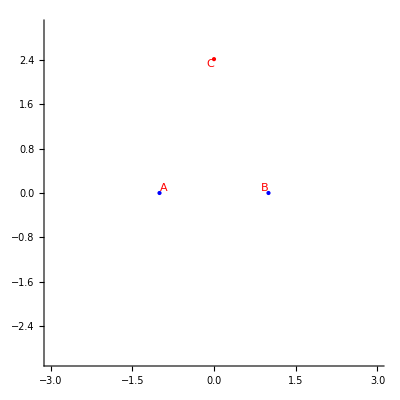

```mathematica
(*Define the points A and B*)A={-1,0};
B={1,0};

(*Since C is vertically aligned with the midpoint of A and B,its x-coordinate is 0. Let C={0,y}.*)

(*Solve for y such that angle ACB=45 degrees.The vectors from C to A and C to B are:CA=A-C={-1,-y} CB=B-C={1,-y} Their dot product is:(-1)*(1)+(-y)*(-y)=-1+y^2,and their magnitudes are both Sqrt[1+y^2].Setting up the equation:(-1+y^2)/(1+y^2)=Cos[45°]=1/Sqrt[2].*)
eq=(y^2-1)/(1+y^2)==1/Sqrt[2];
ySolutions=Solve[eq,y];

(*Simplify the solutions*)
ySolutionsSimplified=Simplify[ySolutions]

(*There are two solutions.For the point above the x-axis,we choose:*)
yValue=1+Sqrt[2];
CC={0,yValue};

(*Verify the angle at C*)
angleACB=VectorAngle[A-CC,B-CC]//N;

Print["The point C is: ",CC];
Print["The angle ACB in degrees is: ",angleACB*180/π];

(*Optionally,plot the points*)
Graphics[{PointSize[Large],Blue,Point[A],Point[B],Red,Point[CC],Text["A",A,{-1,-1}],Text["B",B,{1,-1}],Text["C",CC,{1,1}]},Axes->True,PlotRange->{{-3,3},{-3,3}}]
```

#### gpt garbage

```mathematica
(*The correct center of the arc is at {0,-r},since the arc is part of a circle centered there*)arcCenter={0,-r};

(*Rotate the last point around the true arc center*)
rotatedPoint=RotationTransform[Pi/4,arcCenter][arcPoints[[-1]]];

(*Display the points and rotated point*)
Graphics[{PointSize[Large],Black,Point/@arcPoints,Red,Point[rotatedPoint]}]
```

-Graphics-

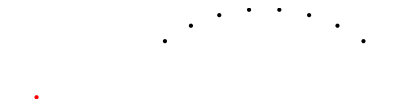

```mathematica
(*Find the actual geometric center of the arc (not just midpoint of two points)*)arcCenter={0,-r};  (*Since the arc is from a circle centered here*)

(*Rotate the MIDDLE point of the arc instead of the last point*)
midIndex=Ceiling[n/2]; (*Middle index*)
rotatedPoint=RotationTransform[Pi/4,arcCenter][arcPoints[[midIndex]]];

(*Display the points and rotated point*)
Graphics[{PointSize[Large],Black,Point/@arcPoints,Red,Point[rotatedPoint]}]
```

```mathematica
(*Correct arc center for rotation*)arcCenter={0,-r};  (*Since the arc is from a circle centered here*)

(*Rotate the ENTIRE arc instead of just one point*)
rotatedArcPoints=RotationTransform[Pi/4,arcCenter]/@arcPoints;

(*Find the new middle point after rotation*)
midIndex=Ceiling[n/2];
rotatedPoint=rotatedArcPoints[[midIndex]];

(*Display the points and rotated point*)
Graphics[{PointSize[Large],Black,Point/@rotatedArcPoints,Red,Point[rotatedPoint]}]
```

-Graphics-

```mathematica
(*Correct arc center for rotation (this is the center of the circle)*)arcCenter={0,-r};

(*Find the actual midpoint BEFORE rotation*)
midIndex=Ceiling[n/2];
trueMidpoint=arcPoints[[midIndex]]; (*This is the correct center point*)

(*Rotate the ENTIRE arc around its center*)
rotatedArcPoints=RotationTransform[Pi/4,arcCenter]/@arcPoints;

(*Rotate the true midpoint correctly*)
rotatedMidpoint=RotationTransform[Pi/4,arcCenter][trueMidpoint];

(*Display the points and rotated midpoint*)
Graphics[{PointSize[Large],Black,Point/@rotatedArcPoints,Red,Point[rotatedMidpoint] (*Now the midpoint should align correctly*)}]
```

-Graphics-

### Gpt vers

```mathematica
anglePointsOnPerpMidline[A_,B_,angleDeg_]:=Module[{M,v,p,t,eq,sol},(*Midpoint of A and B*)M=(A+B)/2;
(*Vector from A to B*)v=B-A;
(*A perpendicular vector to v*)p={v[[2]],-v[[1]]};
(*Define C(t)=M+t p.We want angle ACB=angleDeg.That is,(CA·CB)/(|CA||CB|)==cos(angleDeg).*)eq=((A-(M+t p)).(B-(M+t p)))/(Norm[A-(M+t p)] Norm[B-(M+t p)])==Cos[angleDeg Degree];
(*Solve for t in the reals*)sol=Solve[eq,t,Reals]//Simplify;
(*Substitute solutions for t back into C(t)*)(M+t p)/. sol]
```

```mathematica
N/@angleChecks
```

{45.,45.}

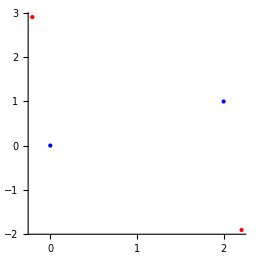

```mathematica
A={0,0};
B={2,1};
angleDeg=45;

solPoints=anglePointsOnPerpMidline[A,B,angleDeg];

(*Numeric check of angles at each solution*)
angleChecks=VectorAngle[A-#,B-#]*180/Pi&/@solPoints;

Graphics[{PointSize[Large],Blue,Point[A],Point[B],Red,Point[solPoints]},Axes->True,PlotRange->All,AspectRatio->1]
```

{{{1-1/2 √(3+2 √2),1/2+√(3+2 √2)},{1+1/2 √(3+2 √2),1/2-√(3+2 √2)}},{(180 ArcCos[((-1/2-√(3+2 √2)) (1/2-√(3+2 √2))+(-1+1/2 √(3+2 √2)) (1+1/2 √(3+2 √2)))/(√(((1+1/2 √(3+2 √2))^2+(-1/2+√(3+2 √2))^2) ((-1+1/2 √(3+2 √2))^2+(1/2+√(3+2 √2))^2)))])/π,(180 ArcCos[((-1-1/2 √(3+2 √2)) (1-1/2 √(3+2 √2))+(-1/2+√(3+2 √2)) (1/2+√(3+2 √2)))/(√(((1+1/2 √(3+2 √2))^2+(-1/2+√(3+2 √2))^2) ((-1+1/2 √(3+2 √2))^2+(1/2+√(3+2 √2))^2)))])/π}}

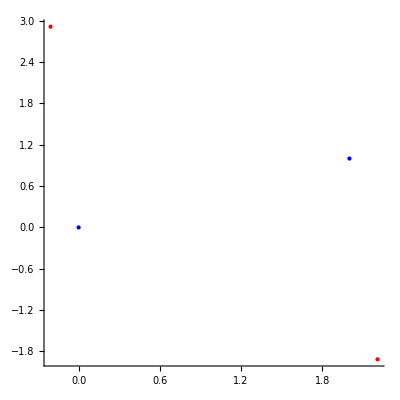

```mathematica
anglePointsOnPerpMidline[A_,B_,angleDeg_]:=Module[{M,v,p,t,eq,sol},M=(A+B)/2;
v=B-A;
p={v[[2]],-v[[1]]};(*Perp to v*)eq=((A-(M+t p)).(B-(M+t p)))/(Norm[A-(M+t p)] Norm[B-(M+t p)])==Cos[angleDeg Degree];
sol=Solve[eq,t,Reals]//Simplify;
(M+t p)/. sol]

(*Example usage*)
A={0,0};
B={2,1};
angleDeg=45;

(*Get the solution points C on the perpendicular at midpoint that yield angle ACB=45°*)
solPoints=anglePointsOnPerpMidline[A,B,angleDeg];

(*Numerically check each solution's angle ACB*)
angleChecks=VectorAngle[A-#,B-#]*180/Pi&/@solPoints;

(*Show the results*)
{solPoints,angleChecks}

Graphics[{PointSize[Large],Blue,Point[A],Point[B],Red,Point[solPoints]},Axes->True,PlotRange->All,AspectRatio->1   (*Important so angles look correct visually*)]
```

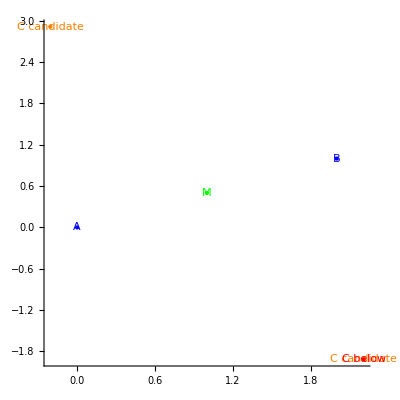

```mathematica
(*1) Define the function that returns ALL solutions on the perpendicular through the midpoint of A,B that yield angle ACB=angleDeg.*)Clear[anglePointsOnPerpMidline];
anglePointsOnPerpMidline[A_,B_,angleDeg_]:=Module[{M,v,p,t,eq,sol},(*Midpoint*)M=(A+B)/2;
(*Vector from A to B,and a perpendicular vector p*)v=B-A;
p={v[[2]],-v[[1]]};
(*We parametrize C(t)=M+t p,then require angle ACB=angleDeg.*)eq=((A-(M+t p)).(B-(M+t p)))/(Norm[A-(M+t p)] Norm[B-(M+t p)])==Cos[angleDeg Degree];
(*Solve for t in the reals*)sol=Solve[eq,t,Reals]//Simplify;
(*Return points {Mx+t px,My+t py} for each real solution*)(M+t p)/. sol];

(*2) Example usage*)
A={0,0};
B={2,1};
angleDeg=45;

(*Get all possible solutions on the perpendicular through midpoint*)
allSolutions=anglePointsOnPerpMidline[A,B,angleDeg];

(*Midpoint for reference*)
M=(A+B)/2;

(*3) Pick the solution "below" in terms of smaller y than the midpoint*)
belowSolution=Select[allSolutions,#[[2]]<M[[2]]&];

(*Verify the angles numerically*)
angleChecksAll=VectorAngle[A-#,B-#]*180/Pi&/@allSolutions;
angleCheckBelow=VectorAngle[A-#,B-#]*180/Pi&/@belowSolution;

(*4) Plot and label everything*)
Graphics[{PointSize[Large],(*Original points A and B,in blue*)Blue,Point[A],Point[B],Text["A",A,{-1,0}],Text["B",B,{1,0}],(*Midpoint M,in green*)Green,Point[M],Text["M",M,{0,-1}],(*All candidate solutions,in orange*)Orange,Point[allSolutions],Map[Text["C candidate",#,{0,1}]&,allSolutions],(*The "below" solution in red*)Red,Point[belowSolution],Map[Text["C below",#,{0,-1}]&,belowSolution]},Axes->True,PlotRange->All,AspectRatio->1]
```

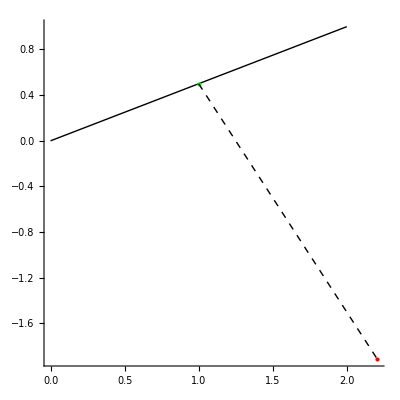

```mathematica
ClearAll[anglePointsOnPerpMidline];

anglePointsOnPerpMidline[A_,B_,angleDeg_]:=Module[{M,v,p,t,eq,sol},M=(A+B)/2;(*midpoint of A and B*)v=B-A;(*vector from A to B*)p={v[[2]],-v[[1]]};(*a perpendicular vector to v*)(*Parametric form C(t)=M+t p;impose angle ACB=angleDeg*)eq=((A-(M+t p)).(B-(M+t p)))/(Norm[A-(M+t p)] Norm[B-(M+t p)])==Cos[angleDeg Degree];
sol=Solve[eq,t,Reals]//Simplify;
(M+t p)/. sol];

(*Example points and desired angle*)
A={0,0};
B={2,1};
angleDeg=45;

(*Find all solutions on the perpendicular through midpoint*)
allSolutions=anglePointsOnPerpMidline[A,B,angleDeg];
M=(A+B)/2;

(*Pick just the one'below' the midpoint in terms of y-coordinate*)
belowSolution=Select[allSolutions,#[[2]]<M[[2]]&];
(*This might return one or zero or multiple points;
typically there's exactly one.We'll assume exactly one here.*)

(*Numeric check of the angle at that point*)
angleCheckBelow=VectorAngle[A-belowSolution[[1]],B-belowSolution[[1]]]*180/Pi;

Graphics[{(*Draw the segment AB in black,thick*)Thick,Black,Line[{A,B}],(*Mark the midpoint M in green*)Green,Point[M],(*Label or not,as you prefer.Example:Text["M",M,{0,-0.2}]*)(*Draw the perpendicular line from M to the chosen below solution*)Dashed,Black,Line[{M,belowSolution[[1]]}],(*Draw the solution point in red*)Red,PointSize[Large],Point[belowSolution[[1]]]},Axes->True,PlotRange->All,AspectRatio->1]
```

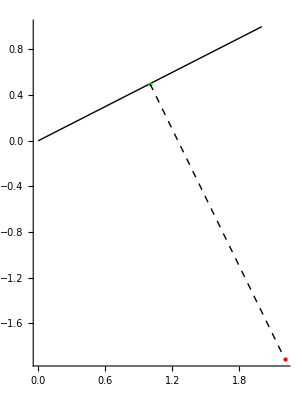

```mathematica
ClearAll[anglePointsOnPerpMidline];

anglePointsOnPerpMidline[A_,B_,angleDeg_]:=Module[{M,v,p,t,eq,sol},M=(A+B)/2;(*midpoint of A and B*)v=B-A;(*vector from A to B*)p={v[[2]],-v[[1]]};(*a perpendicular vector to v*)(*C(t)=M+t p;impose angle ACB=angleDeg*)eq=((A-(M+t p)).(B-(M+t p)))/(Norm[A-(M+t p)] Norm[B-(M+t p)])==Cos[angleDeg Degree];
sol=Solve[eq,t,Reals]//Simplify;
(M+t p)/. sol];

(*Example points*)
A={0,0};
B={2,1};

(*Angle at C we want*)
angleDeg=45;

(*All solutions on the perpendicular at M*)
allSolutions=anglePointsOnPerpMidline[A,B,angleDeg];
M=(A+B)/2;

(*Pick the solution'below' the midpoint in terms of y<M[[2]]*)
belowSolution=Select[allSolutions,#[[2]]<M[[2]]&];

(*Numeric check:angle ACB should be 45 degrees*)
angleCheck=VectorAngle[A-belowSolution[[1]],B-belowSolution[[1]]]*180/Pi;

(*Also check that M->C is perpendicular to A->B*)
perpCheck=VectorAngle[B-A,belowSolution[[1]]-M]*180/Pi;

Graphics[{Thick,Black,Line[{A,B}],(*segment AB*)Green,Point[M],(*midpoint M*)Dashed,Black,Line[{M,belowSolution[[1]]}],Red,PointSize[Large],Point[belowSolution[[1]]]},Axes->True,PlotRange->All]
```

```mathematica
PlanarAngle[{1, 1/2}->{{2, 1}, belowSolution[[1]]}]
```

(3 π)/2

```mathematica
N[(3 π)/(2 °)]
```

270.

```mathematica
belowSolution
```

{{1+1/2 √(3+2 √2),1/2-√(3+2 √2)}}

```mathematica
VectorAngle[{2,1},{0,1}]
```

π/2

```mathematica
perpCheck
```

90

```mathematica
perpCheck=VectorAngle[B-A,belowSolution[[1]]-M]*180/Pi
```

90

```mathematica
B-A
```

{2,1}

```mathematica
B
```

{2,1}

```mathematica
A
```

{0,0}

```mathematica
M
```

{1,1/2}

```mathematica
belowSolution
```

{{1+1/2 √(3+2 √2),1/2-√(3+2 √2)}}

### Gpt clean

```mathematica
anglePointsOnPerpMidline[A_,B_,angleDeg_]:=Module[{M,v,p,t,eq,sol},M=(A+B)/2;
v=B-A;
p={v[[2]],-v[[1]]};
eq=((A-(M+t p)).(B-(M+t p)))/(Norm[A-(M+t p)] Norm[B-(M+t p)])==Cos[angleDeg Degree];
sol=Solve[eq,t,Reals]//Simplify;
(M+t p)/. sol];

A={0,0};
B={2,1};
angleDeg=45;

allSolutions=anglePointsOnPerpMidline[A,B,angleDeg];
M=(A+B)/2;
belowSolution=Select[allSolutions,#[[2]]<M[[2]]&];

angleCheck=VectorAngle[A-belowSolution[[1]],B-belowSolution[[1]]]*180/Pi;
perpCheck=VectorAngle[B-A,belowSolution[[1]]-M]*180/Pi;

Graphics[{Thick,Black,Line[{A,B}],Green,Point[M],Dashed,Black,Line[{M,belowSolution[[1]]}],Red,PointSize[Large],Point[belowSolution[[1]]]},Axes->True,PlotRange->All]
```

-Graphics-

```mathematica
ClearAll[anglePointsOnPerpMidline,recursiveCPoints]
anglePointsOnPerpMidline[A_,B_,angleDeg_]:=Module[{M,v,p,t,eq,sol},M=(A+B)/2;
v=B-A;
p={v[[2]],-v[[1]]};
eq=((A-(M+t p)).(B-(M+t p)))/(Norm[A-(M+t p)] Norm[B-(M+t p)])==Cos[angleDeg Degree];
sol=Solve[eq,t,Reals]//Simplify;
(M+t p)/. sol]
```

```mathematica
recursiveCPoints[pts_List,angleDeg_]:=Module[{sorted,A,B,M,allSolutions,belowSolution,C,leftPts,rightPts,leftRes,rightRes},sorted=SortBy[pts,First];
A=First[sorted];
B=Last[sorted];
If[Length[sorted]<=2,Return[{A,B}]];
M=(A+B)/2;
allSolutions=anglePointsOnPerpMidline[A,B,angleDeg];
belowSolution=Select[allSolutions,#[[2]]<M[[2]]&];
If[belowSolution==={},Return[{A,B}]];
C=belowSolution[[1]];
leftPts=Select[sorted,#[[1]]<=C[[1]]&];
rightPts=Select[sorted,#[[1]]>=C[[1]]&];
leftRes=recursiveCPoints[leftPts,angleDeg];
rightRes=recursiveCPoints[rightPts,angleDeg];
Join[Most[leftRes],rightRes]]
```

```mathematica
targetPoints={{0,0},{0.5,0.2},{1,0.1},{1.5,-0.1},{2,1}};
result=recursiveCPoints[targetPoints,45];
Graphics[{Blue,PointSize[Medium],Point/@targetPoints,Red,Line[result]},Axes->True,AspectRatio->1]
```

$Aborted

-Graphics-

```mathematica
ClearAll[anglePointsOnPerpMidline,recursiveCPoints]
anglePointsOnPerpMidline[A_,B_,angleDeg_]:=Module[{M,v,p,t,eq,sol},M=(A+B)/2;
v=B-A;
p={v[[2]],-v[[1]]};
eq=((A-(M+t p)).(B-(M+t p)))/(Norm[A-(M+t p)] Norm[B-(M+t p)])==Cos[angleDeg Degree];
sol=Solve[eq,t,Reals]//Simplify;
(M+t p)/. sol]
recursiveCPoints[pts_List,angleDeg_]:=Module[{sorted,A,B,M,allSolutions,belowSolution,C,leftPts,rightPts,leftRes,rightRes},sorted=SortBy[pts,First];
A=First[sorted];
B=Last[sorted];
If[Length[sorted]<=2,Return[{A,B}]];
M=(A+B)/2;
allSolutions=anglePointsOnPerpMidline[A,B,angleDeg];
belowSolution=Select[allSolutions,#[[2]]<M[[2]]&];
If[belowSolution==={},Return[{A,B}]];
C=belowSolution[[1]];
leftPts=Select[sorted,#[[1]]<=C[[1]]&];
rightPts=Select[sorted,#[[1]]>=C[[1]]&];
leftRes=recursiveCPoints[leftPts,angleDeg];
rightRes=recursiveCPoints[rightPts,angleDeg];
Join[Most[leftRes],rightRes]]
r=1;
theta1=0;
theta2=Pi;
n=8;
arcPoints=Table[{r Sin[θ],-r Cos[θ]},{θ,theta1,theta2,(theta2-theta1)/(n-1)}];
result=recursiveCPoints[arcPoints,45];
Graphics[{Blue,PointSize[Medium],Point/@arcPoints,Red,Line[result]},Axes->True,AspectRatio->1]
```

$Aborted

-Graphics-

```mathematica
ClearAll[anglePointsOnPerpMidline,recursiveCPoints]
anglePointsOnPerpMidline[A_,B_,angleDeg_]:=Module[{M,v,p,t,eq,sol},M=(A+B)/2;
v=B-A;
p={v[[2]],-v[[1]]};
eq=((A-(M+t p)).(B-(M+t p)))/(Norm[A-(M+t p)] Norm[B-(M+t p)])==Cos[angleDeg Degree];
sol=Solve[eq,t,Reals]//Simplify;
(M+t p)/. sol]
recursiveCPoints[pts_List,angleDeg_]:=Module[{sorted,A,B,M,allSolutions,belowSolution,C,leftPts,rightPts,leftRes,rightRes},sorted=SortBy[pts,First];
A=First[sorted];
B=Last[sorted];
If[Length[sorted]<=2,Return[{A,B}]];
M=(A+B)/2;
allSolutions=anglePointsOnPerpMidline[A,B,angleDeg];
belowSolution=Select[allSolutions,#[[2]]<M[[2]]&];
If[belowSolution==={},Return[{A,B}]];
C=belowSolution[[1]];
leftPts=Select[sorted,#[[1]]<=C[[1]]&];
rightPts=Select[sorted,#[[1]]>=C[[1]]&];
leftRes=recursiveCPoints[leftPts,angleDeg];
rightRes=recursiveCPoints[rightPts,angleDeg];
Join[Most[leftRes],rightRes]]
```

```mathematica
res = recursiveCPoints[arcPoints, 45];
```

$Aborted

```mathematica
r=1;theta1=0;theta2=Pi;n=8;
arcPoints=Table[{r Sin[θ],-r Cos[θ]},{θ,theta1,theta2,(theta2-theta1)/(n-1)}];
result=recursiveCPoints[arcPoints,45];
Graphics[{Blue,PointSize[Medium],Point/@arcPoints,Red,Line[result]},Axes->True,AspectRatio->1]
```

$Aborted

-Graphics-

π

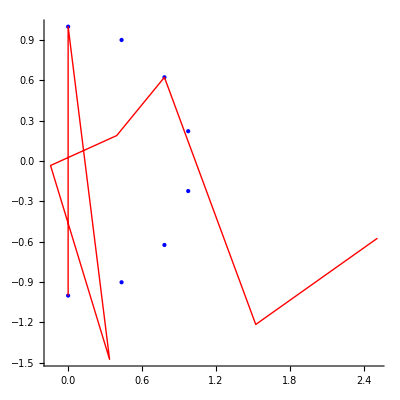

```mathematica
ClearAll[anglePointsOnPerpMidline,recursiveCPoints]

(*Computes all points C on the perpendicular through the midpoint of A,B such that angle ACB=angleDeg.Usually returns two points (above/below).*)
anglePointsOnPerpMidline[A_,B_,angleDeg_]:=Module[{M,v,p,t,eq,sol},M=(A+B)/2;
v=B-A;
p={v[[2]],-v[[1]]};
eq=((A-(M+t p)).(B-(M+t p)))/(Norm[A-(M+t p)] Norm[B-(M+t p)])==Cos[angleDeg Degree];
sol=Solve[eq,t,Reals]//Simplify;
(M+t p)/. sol];

(*Recursively build a polyline by splitting on the "below" solution.-Sort by x.-If≤2 points,just return them.-Otherwise pick leftmost(A),rightmost(B).-Find new C (the "below" solution).-Split the MIDDLE points into leftPts and rightPts.-Recursively connect each subset,adding A or B to its ends.-Then join everything into one polyline with C in the middle.*)
recursiveCPoints[pts_List,angleDeg_]:=Module[{sorted,A,B,middle,M,allSolutions,belowSolution,C,leftPts,rightPts,leftRes,rightRes},sorted=SortBy[pts,First];
(*If there are≤2 points,nothing more to do.*)If[Length[sorted]<=2,Return[sorted]];
A=First[sorted];
B=Last[sorted];
(*The "middle" points exclude A and B so the recursion shrinks.*)middle=Most[Rest[sorted]];
M=(A+B)/2;
allSolutions=anglePointsOnPerpMidline[A,B,angleDeg];
belowSolution=Select[allSolutions,#[[2]]<M[[2]]&];
(*If there's no "below" solution,just return the endpoints.*)If[belowSolution==={},Return[{A,B}]];
(*Pick the first "below" solution,or you could pick e.g.last,etc.*)C=belowSolution[[1]];
(*Split the MIDDLE points around C's x-coordinate.*)leftPts=Select[middle,#[[1]]<=C[[1]]&];
rightPts=Select[middle,#[[1]]>=C[[1]]&];
(*Recurse on each subset,re-attaching A or B at the boundary.*)leftRes=recursiveCPoints[Prepend[leftPts,A],angleDeg];
rightRes=recursiveCPoints[Append[rightPts,B],angleDeg];
(*Combine into a single polyline:leftRes goes from A... up to something,then we insert C,then continue with rightRes from B down to something.*)Join[leftRes,{C},Rest[rightRes]]];

(*Example:arcPoints from θ1=0 to θ2=π,in n=8 steps*)
r=1;theta1=0;theta2=Pi;n=8;
arcPoints=Table[{r Sin[θ],-r Cos[θ]},{θ,theta1,theta2,(theta2-theta1)/(n-1)}];

(*Build the polyline*)
result=recursiveCPoints[arcPoints,45];

(*Show the original points and the resulting line*)
Graphics[{Blue,PointSize[Medium],Point/@arcPoints,Red,Line[result]},Axes->True,AspectRatio->1]
```

```mathematica
θ1=Pi-(Pi/5);  (*Start angle:symmetric around π*)
θ2=Pi+(Pi/5);  (*End angle*)
r=5;             (*Radius*)
n=8;             (*Number of points*)

arcPoints=Table[{r Sin[θ],-r Cos[θ]},(*Ensure symmetry with respect to π*){θ,θ1,θ2,(θ2-θ1)/(n-1)}];
```

$Aborted

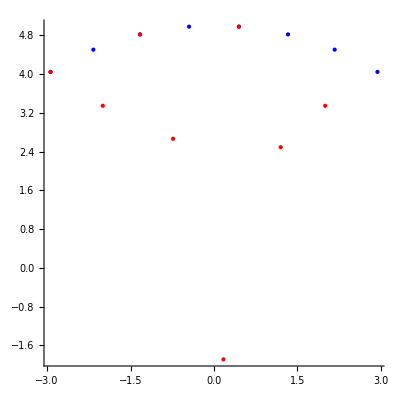

```mathematica
(*Build the polyline*)
result=recursiveCPoints[arcPoints,45];

(*Show the original points and the resulting line*)
Graphics[{Blue,PointSize[Medium],Point/@arcPoints,Red,Point/@result},Axes->True,AspectRatio->1]
```

```mathematica
ClearAll[anglePointsOnPerpMidline,buildTree]

anglePointsOnPerpMidline[A_,B_,angleDeg_]:=Module[{M,v,p,t,eq,sol},M=(A+B)/2;
v=B-A;
p={v[[2]],-v[[1]]};
eq=((A-(M+t p)).(B-(M+t p)))/(Norm[A-(M+t p)] Norm[B-(M+t p)])==Cos[angleDeg Degree];
sol=Solve[eq,t,Reals]//Simplify;
(M+t p)/. sol]

buildTree[pts_List,angleDeg_]:=Module[{n,A,B,M,allSol,belowSol,c,mid,leftPts,rightPts,linesLeft,linesRight,rootLeft,rootRight,lines},n=Length[pts];
If[n==1,Return[{{},pts[[1]]}]];
A=First[pts];
B=Last[pts];
If[n==2,M=(A+B)/2;
allSol=anglePointsOnPerpMidline[A,B,angleDeg];
belowSol=Select[allSol,#[[2]]<M[[2]]&];
If[belowSol==={},Return[{{Line[{A,B}]},A}],c=belowSol[[1]];
Return[{{Line[{c,A}],Line[{c,B}]},c}]]];
M=(A+B)/2;
allSol=anglePointsOnPerpMidline[A,B,angleDeg];
belowSol=Select[allSol,#[[2]]<M[[2]]&];
If[belowSol==={},Return[{{Line[{A,B}]},A}]];
c=belowSol[[1]];
mid=Floor[(n-2)/2];
leftPts=pts[[2;;1+mid]];
rightPts=pts[[2+mid;;n-1]];
{linesLeft,rootLeft}=buildTree[leftPts,angleDeg];
{linesRight,rootRight}=buildTree[rightPts,angleDeg];
lines=Join[linesLeft,linesRight,{Line[{c,A}],Line[{c,B}],Line[{c,rootLeft}],Line[{c,rootRight}]}];
{lines,c}]
```

```mathematica
{treeLines,rootNode}=buildTree[arcPoints,45];
```

First::nofirst: {} has zero length and no first element.

Last::nolast: {} has zero length and no last element.

$Aborted

```mathematica
Graphics[{Blue,PointSize[Medium],Point/@arcPoints,Red,treeLines},Axes->True,AspectRatio->1]
```

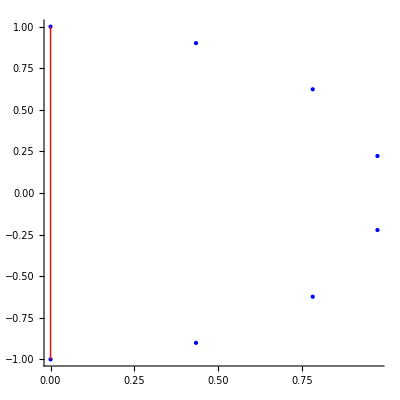

```mathematica
ClearAll[anglePointsOnPerpMidline,buildTree]

anglePointsOnPerpMidline[A_,B_,angleDeg_]:=Module[{M,v,p,t,eq,sol},M=(A+B)/2;
v=B-A;
p={v[[2]],-v[[1]]};
eq=((A-(M+t p)).(B-(M+t p)))/(Norm[A-(M+t p)] Norm[B-(M+t p)])==Cos[angleDeg Degree];
sol=Solve[eq,t,Reals]//Simplify;
(M+t p)/. sol]

buildTree[pts_List,angleDeg_]:=Module[{n,A,B,M,allSol,belowSol,c,mid,leftPts,rightPts,linesLeft,linesRight,rootLeft,rootRight,lines},n=Length[pts];
If[n==1,Return[{{},pts[[1]]}]];
A=First[pts];
B=Last[pts];
If[n==2,M=(A+B)/2;
allSol=anglePointsOnPerpMidline[A,B,angleDeg];
belowSol=Select[allSol,#[[2]]<M[[2]]&];
If[belowSol==={},Return[{{Line[{A,B}]},A}],c=belowSol[[1]];
Return[{{Line[{c,A}],Line[{c,B}]},c}]]];
M=(A+B)/2;
allSol=anglePointsOnPerpMidline[A,B,angleDeg];
belowSol=Select[allSol,#[[2]]<M[[2]]&];
If[belowSol==={},Return[{{Line[{A,B}]},A}]];
c=belowSol[[1]];
mid=Floor[(n-2)/2];
leftPts=pts[[2;;1+mid]];
rightPts=pts[[2+mid;;n-1]];
{linesLeft,rootLeft}=buildTree[leftPts,angleDeg];
{linesRight,rootRight}=buildTree[rightPts,angleDeg];
lines=Join[linesLeft,linesRight,{Line[{c,A}],Line[{c,B}],Line[{c,rootLeft}],Line[{c,rootRight}]}];
{lines,c}]

r=1;
theta1=0;
theta2=Pi;
n=8;
arcPoints=Table[{r Sin[θ],-r Cos[θ]},{θ,theta1,theta2,(theta2-theta1)/(n-1)}];
{treeLines,rootNode}=buildTree[arcPoints,45];

Graphics[{Blue,PointSize[Medium],Point/@arcPoints,Red,treeLines},Axes->True,AspectRatio->1]
```

First::nofirst: {} has zero length and no first element.

Last::nolast: {} has zero length and no last element.

First::nofirst: {} has zero length and no first element.

Last::nolast: {} has zero length and no last element.

$Aborted

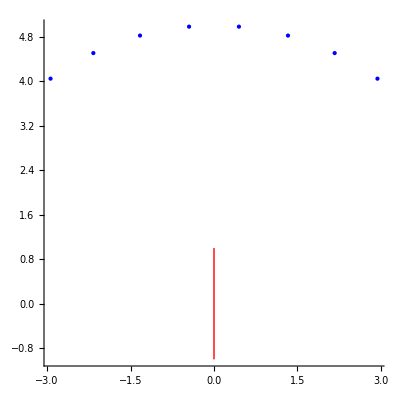

```mathematica
ClearAll[anglePointsOnPerpMidline,buildTree]

anglePointsOnPerpMidline[A_,B_,angleDeg_]:=Module[{M,v,p,t,eq,sol},M=(A+B)/2;
v=B-A;
p={v[[2]],-v[[1]]};
eq=((A-(M+t p)).(B-(M+t p)))/(Norm[A-(M+t p)] Norm[B-(M+t p)])==Cos[angleDeg Degree];
sol=Solve[eq,t,Reals]//Simplify;
(M+t p)/. sol]

buildTree[pts_List,angleDeg_]:=Module[{n,A,B,M,allSol,belowSol,c,mid,leftPts,rightPts,linesLeft,linesRight,rootLeft,rootRight,lines},n=Length[pts];
If[n==1,Return[{{},pts[[1]]}]];
A=First[pts];
B=Last[pts];
If[n==2,M=(A+B)/2;
allSol=anglePointsOnPerpMidline[A,B,angleDeg];
belowSol=Select[allSol,#[[2]]<M[[2]]&];
If[belowSol==={},Return[{{Line[{A,B}]},A}],c=belowSol[[1]];
Return[{{Line[{c,A}],Line[{c,B}]},c}]]];
M=(A+B)/2;
allSol=anglePointsOnPerpMidline[A,B,angleDeg];
belowSol=Select[allSol,#[[2]]<M[[2]]&];
If[belowSol==={},Return[{{Line[{A,B}]},A}]];
c=belowSol[[1]];
mid=Floor[(n-2)/2];
leftPts=pts[[2;;1+mid]];
rightPts=pts[[2+mid;;n-1]];
{linesLeft,rootLeft}=buildTree[leftPts,angleDeg];
{linesRight,rootRight}=buildTree[rightPts,angleDeg];
lines=Join[linesLeft,linesRight,{Line[{c,A}],Line[{c,B}],Line[{c,rootLeft}],Line[{c,rootRight}]}];
{lines,c}]
theta1=Pi-(Pi/5);
theta2=Pi+(Pi/5);
r=5;
n=8;
arcPoints=Table[{r Sin[θ],-r Cos[θ]},{θ,theta1,theta2,(theta2-theta1)/(n-1)}];

{treeLines,rootNode}=buildTree[arcPoints,45];

Graphics[{Blue,PointSize[Medium],Point/@arcPoints,Red,treeLines},Axes->True,AspectRatio->1]
```

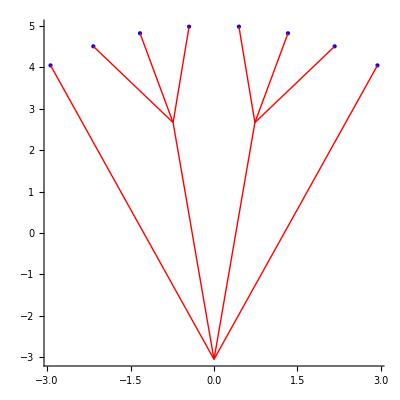

```mathematica
ClearAll[anglePointsOnPerpMidline,buildTree]

(*Finds all points C on the perpendicular through the midpoint of A,B so that angle ACB=angleDeg.Typically returns 0,1,or 2 points.*)
anglePointsOnPerpMidline[A_,B_,angleDeg_]:=Module[{M,v,p,t,eq,sol},M=(A+B)/2;
v=B-A;
p={v[[2]],-v[[1]]};
eq=((A-(M+t p)).(B-(M+t p)))/(Norm[A-(M+t p)] Norm[B-(M+t p)])==Cos[angleDeg Degree];
sol=Solve[eq,t,Reals]//Simplify;
(M+t p)/. sol];

(*Builds a "tree" of lines by:-Taking the first point as A and last point as B in the list.-Finding a "below" point C between A and B if it exists.-Recursively building sub-trees from the remaining middle points.-Returns {listOfLines,rootPoint}.If no root exists (empty list),returns {{},Null}.*)
buildTree[pts_List,angleDeg_]:=Module[{n=Length[pts],A,B,M,allSol,belowSol,c,mid,leftPts,rightPts,linesLeft,linesRight,rootLeft,rootRight,lines},(*Base case:no points=>no lines,no root*)If[n==0,Return[{{},Null}]];
(*Base case:exactly 1 point=>no lines,that single point is the root*)If[n==1,Return[{{},pts[[1]]}]];
A=First[pts];
B=Last[pts];
(*Base case:exactly 2 points=>either connect them directly or via C*)If[n==2,M=(A+B)/2;
allSol=anglePointsOnPerpMidline[A,B,angleDeg];
belowSol=Select[allSol,#[[2]]<M[[2]]&];
If[belowSol==={},(*No perpendicular solution=>just one line A-B,root=A or B.Typically you'd pick one root.We'll pick A for definiteness.*)Return[{{Line[{A,B}]},A}],(*If there's a "below" solution,connect it to A and B.The new root is that solution C.*)c=First[belowSol];
Return[{{Line[{c,A}],Line[{c,B}]},c}]]];
(*Now n>=3*)M=(A+B)/2;
allSol=anglePointsOnPerpMidline[A,B,angleDeg];
belowSol=Select[allSol,#[[2]]<M[[2]]&];
(*If no below solution=>just connect A-B,pick A as root (arbitrary).*)If[belowSol==={},Return[{{Line[{A,B}]},A}]];
c=First[belowSol];
(*Split the middle points (excluding A,B) roughly in half*)mid=Floor[(n-2)/2];
leftPts=pts[[2;;1+mid]];
rightPts=pts[[2+mid;;n-1]];
(*Recursively build sub-trees*){linesLeft,rootLeft}=buildTree[leftPts,angleDeg];
{linesRight,rootRight}=buildTree[rightPts,angleDeg];
(*Combine lines.We'll only connect c->rootLeft if rootLeft!=Null.Same for rootRight.*)lines=Join[linesLeft,linesRight,{Line[{c,A}],Line[{c,B}]},If[rootLeft===Null,{},{Line[{c,rootLeft}]}],If[rootRight===Null,{},{Line[{c,rootRight}]}]];
{lines,c}];

(*Example arc points*)
theta1=Pi-(Pi/5);
theta2=Pi+(Pi/5);
r=5;
n=8;
arcPoints=Table[{r Sin[θ],-r Cos[θ]},{θ,theta1,theta2,(theta2-theta1)/(n-1)}
];

(*Build the "tree"*)
{treeLines,rootNode}=buildTree[arcPoints,45];

Graphics[{Blue,PointSize[Medium],Point/@arcPoints,Red,treeLines},Axes->True,AspectRatio->1]
```

```mathematica
ClearAll[anglePointsOnPerpMidline,buildBinaryTree]

(*Finds all points C on the perpendicular through the midpoint of A,B so that angle ACB=angleDeg.Typically returns 0,1,or 2 points.*)
anglePointsOnPerpMidline[A_,B_,angleDeg_]:=Module[{M,v,p,t,eq,sol},M=(A+B)/2;
v=B-A;
p={v[[2]],-v[[1]]};
eq=((A-(M+t p)).(B-(M+t p)))/(Norm[A-(M+t p)] Norm[B-(M+t p)])==Cos[angleDeg Degree];
sol=Solve[eq,t,Reals]//Simplify;
(M+t p)/. sol];

(*Recursively builds a perfect "binary tree" whose leaves are the given pts.-If there's 1 point,it's a leaf;no internal node is created.-Otherwise,split into left half and right half,build subtrees.-Create a new internal node C so angle=angleDeg between leftRoot& rightRoot.-Return {listOfLines,rootCoordinate}.*)
buildBinaryTree[pts_List,angleDeg_]:=Module[{n,half,linesLeft,rootLeft,linesRight,rootRight,M,allSol,belowSol,c,lines},n=Length[pts];
(*If no points,return "empty subtree"*)If[n==0,Return[{{},Null}]];
(*If exactly one point,it's a leaf*)If[n==1,Return[{{},pts[[1]]}]];
(*Split into two halves*)half=Floor[n/2];
{linesLeft,rootLeft}=buildBinaryTree[pts[[1;;half]],angleDeg];
{linesRight,rootRight}=buildBinaryTree[pts[[half+1;;n]],angleDeg];
(*If one side is empty,just connect everything to the non-empty side*)If[rootLeft===Null||rootRight===Null,Return[{Join[linesLeft,linesRight],If[rootLeft=!=Null,rootLeft,rootRight]}];];
(*Find a new internal node C so that angle at C is angleDeg between rootLeft and rootRight.We pick the "below" solution.*)M=(rootLeft+rootRight)/2;
allSol=anglePointsOnPerpMidline[rootLeft,rootRight,angleDeg];
belowSol=Select[allSol,#[[2]]<M[[2]]&];
(*If no "below" solution,just connect rootLeft->rootRight directly*)If[belowSol==={},Return[{Join[linesLeft,linesRight,{Line[{rootLeft,rootRight}]}],rootLeft}]];
(*Otherwise,pick the first below solution as our new internal node*)c=First[belowSol];
(*Combine all lines:the subtrees plus the 2 new edges from C*)lines=Join[linesLeft,linesRight,{Line[{c,rootLeft}],Line[{c,rootRight}]}];
{lines,c}];

(*Example arc points,as given in your last message*)
theta1=Pi-(Pi/5);
theta2=Pi+(Pi/5);
r=5;
n=8;
arcPoints=Table[{r Sin[θ],-r Cos[θ]},{θ,theta1,theta2,(theta2-theta1)/(n-1)}
];

(*Build the binary tree*)
{treeLines,rootNode}=buildBinaryTree[arcPoints,45];

Graphics[{Blue,PointSize[Medium],Point/@arcPoints,Red,treeLines},Axes->True,AspectRatio->1]
```

$Aborted

-Graphics-

```mathematica
anglePointsOnPerpMidline[A_,B_,angleDeg_]:=Module[{M,v,p,t,eq,sol},
M=(A+B)/2;
v=B-A;
p={v[[2]],-v[[1]]};
eq=((A-(M+t p)).(B-(M+t p)))/(Norm[A-(M+t p)] Norm[B-(M+t p)])==Cos[angleDeg Degree];
sol=Solve[eq,t,Reals]//Simplify;
(M+t p)/. sol];
```

```mathematica
start = {0, -5};
```

```mathematica
theta1=Pi-(Pi/5);
theta2=Pi+(Pi/5);
r=5;
n=8;
arcPoints=Table[{r Sin[θ],-r Cos[θ]},{θ,theta1,theta2,(theta2-theta1)/(n-1)}];
```

```mathematica
First[anglePointsOnPerpMidline[arcPoints[[1]], arcPoints[[-1]], 45]]
```

{0,-5/4 (-1-√5)-5 √((3+2 √2) (5/8-(√5)/8))}

```mathematica
Graphics[{PointSize[Large], Point[], Sequence[Point/@arcPoints], Point[start]} ]
```

-Graphics-

```mathematica
Length[Partition[arcPoints, Length[arcPoints] / 2]]
```

2

```mathematica
First[anglePointsOnPerpMidline[#[[1]], #[[-1]], 45]]&/@N[Partition[arcPoints, Length[arcPoints] / 2]]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{0.565174,1.5059},{-0.565174,1.5059}}

```mathematica
First[anglePointsOnPerpMidline[#[[1]], #[[-1]], 45]]&/@N[Partition[arcPoints, Length[arcPoints] / 4]]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

{{1.99919,3.34609},{0.695984,3.83519},{-0.695984,3.83519},{-1.99919,3.34609}}

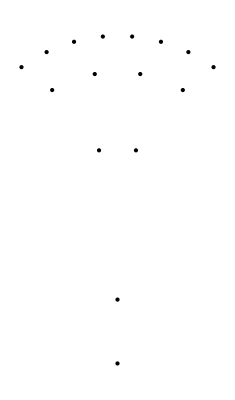

```mathematica
Graphics[{PointSize[Large], Point[], Sequence[Point/@arcPoints], Point[start], Point[],Point[]} ]
```

```mathematica
sowbranchpts[pts_, deg_]:= 
With[{new  = Quiet[First[anglePointsOnPerpMidline[#[[1]], #[[-1]], deg]]&[N[pts]]]},
Sow[new, ToString@Length[pts]];
If[Length[pts] == 2, {}, sowbranchpts[#, deg]&/@ Partition[pts, Length[pts] / 2]] ]
```

```mathematica
r = Reap[sowbranchpts[arcPoints, 45]];
```

```mathematica
r[[2]]
```

{{{0.,-3.05011}},{{0.565174,1.5059},{-0.565174,1.5059}},{{1.99919,3.34609},{0.695984,3.83519},{-0.695984,3.83519},{-1.99919,3.34609}}}